## Slowly-rotating neutron stars in generic scalar-tensor theories with a single scalar. P. Pani & E. Berti, arXiv:XXXX

In this notebook we derive and integrate the equations governing the structure of rotating compact star in a generic scalar-tensor theory of gravity to second order in the spin.

```mathematica
Quit[];
```

# Deriving the equations:

## Initialization

The expansion of the metric is the same as discussed by Hartle & Thorne [Astrophys.J. 153, 807 (1968)]:

```mathematica
ClearAll[GM0,x,g,ϕ,ϕ0,Λ,Ψ,α,γ,Y,Σ,Δ,NN,ω,Δ,Σ,gff,gtt,ϕ,M,F,V,f0,f1,f2,f3,f4,Ω,A,ϕ,B,ζ,ϕ,Φ1,ω,X,r,u]
$Assumptions={r≥0,θ≥0,θ≤π,J≥0,NN≥0,rh≥0,X≥0};
x={t,r,θ,φ};

ω[r_]:=Ω-ω1[r];

P2[θ_]:=(3(1-X[θ])-1)/2;
gdd0={{-Exp[ν[r]](1+ϵa^2 2(h0[r]+h2[r] P2[θ]))+ϵa^2 ω[r]^2 r^2 X[θ],0,0,-ϵa ω[r] X[θ] r^2},{0,(1-2 M[r]/r)^-1(1+2 ϵa^2(m0[r]+m2[r] P2[θ])/(r-2 M[r])),0,0},{0,0,r^2(1+2 ϵa^2(v2[r]-h2[r])P2[θ]),0},{-ϵa ω[r] X[θ] r^2,0,0,r^2(1+2 ϵa^2(v2[r]-h2[r])P2[θ])X[θ]}};

ORDERa=2;(*order of the expansion in the star's angular velocity*)
ORDERp=0;
```

#### Rule 0th order:

```mathematica
BISERIES[Z_]:=Z/.Union[{X'[θ]^2->4 X[θ](1-X[θ]),X''[θ]->2 (1-2X[θ])}];(*this is just a simple rule for X[θ]=Sin[θ]^2;*)
```

#### Metric and co.

```mathematica
gdd=Simplify[BISERIES[Normal[Series[gdd0,{ϵa,0,ORDERa},{ϵp,0,ORDERp}]]]];
guu=Simplify[BISERIES[Normal[Series[Inverse[gdd],{ϵa,0,ORDERa},{ϵp,0,ORDERp}]]]];
DET=Simplify[BISERIES[Normal[Series[Det[gdd],{ϵa,0,ORDERa},{ϵp,0,ORDERp}]]]];
dim=Length[gdd];
Do[g[i,j]=Simplify[gdd[[i]][[j]]];,{i,1,dim},{j,1,dim}];
MatrixForm[gdd]
MatrixForm[guu]
```

(-ⅇ^ν[r]+ϵa^2 (-ⅇ^ν[r] (2 h0[r]+h2[r] (2-3 X[θ]))+r^2 X[θ] (Ω-ω1[r])^2) | 0 | 0 | r^2 ϵa X[θ] (-Ω+ω1[r])
0 | (r (r-2 M[r]+2 ϵa^2 m0[r]+2 ϵa^2 m2[r]-3 ϵa^2 m2[r] X[θ]))/(r-2 M[r])^2 | 0 | 0
0 | 0 | r^2 (1+ϵa^2 v2[r] (2-3 X[θ])+ϵa^2 h2[r] (-2+3 X[θ])) | 0
r^2 ϵa X[θ] (-Ω+ω1[r]) | 0 | 0 | r^2 X[θ] (1+ϵa^2 (h2[r]-v2[r]) (-2+3 X[θ])))

(ⅇ^(-ν[r]) (-1+2 ϵa^2 h0[r]+ϵa^2 h2[r] (2-3 X[θ])) | 0 | 0 | ⅇ^(-ν[r]) ϵa (-Ω+ω1[r])
0 | 1-(2 M[r])/r+(ϵa^2 (-2 m0[r]+m2[r] (-2+3 X[θ])))/r | 0 | 0
0 | 0 | (1+ϵa^2 h2[r] (2-3 X[θ])+ϵa^2 v2[r] (-2+3 X[θ]))/r^2 | 0
ⅇ^(-ν[r]) ϵa (-Ω+ω1[r]) | 0 | 0 | (1-ⅇ^(-ν[r]) ϵa^2 (ⅇ^ν[r] h2[r] (-2+3 X[θ])-ⅇ^ν[r] v2[r] (-2+3 X[θ])+r^2 X[θ] (Ω-ω1[r])^2))/(r^2 X[θ]))

#### Basic definitions

```mathematica
Do[Christ[i,j,k]=Simplify[BISERIES[Normal[Series[Sum[1/2 guu[[k]][[l]](D[gdd[[l]][[i]],x[[j]]]+D[g[l,j],x[[i]]]-D[g[j,i],x[[l]]]),{l,1,dim}],{ϵa,0,ORDERa},{ϵp,0,ORDERp}]]]];,{i,1,dim},{j,1,dim},{k,1,dim}];
```

```mathematica
Timing[Do[Ruddd[a,i,j,k]=Simplify[BISERIES[Normal[Series[D[Christ[i,k,a],x[[j]]]-D[Christ[i,j,a],x[[k]]]+Sum[Christ[i,k,β]Christ[β,j,a]-Christ[i,j,β]Christ[β,k,a],{β,1,dim}],{ϵa,0,ORDERa},{ϵp,0,ORDERp}]]]];,{a,1,dim},{i,1,dim},{j,1,dim},{k,1,dim}]]
```

{10.4067,Null}

```mathematica
Timing[Do[Ricci[i,k]=Simplify[BISERIES[Normal[Series[Sum[Ruddd[l,i,l,k],{l,1,dim}],{ϵa,0,ORDERa},{ϵp,0,ORDERp}]]]];,{i,1,dim},{k,1,dim}];]
Do[Ruu[i,k]=Simplify[BISERIES[Normal[Series[Sum[Ricci[l,m]guu[[i]][[l]]guu[[k]][[m]],{l,1,dim},{m,1,dim}],{ϵa,0,ORDERa},{ϵp,0,ORDERp}]]]];,{i,1,dim},{k,1,dim}];
SCAL=Simplify[BISERIES[Normal[Series[Sum[guu[[i]][[j]]Ricci[i,j],{i,1,dim},{j,1,dim}],{ϵa,0,ORDERa},{ϵp,0,ORDERp}]]]];
Do[Eins[i,j]=Simplify[BISERIES[Normal[Series[Ricci[i,j]-1/2 SCAL g[i,j],{ϵa,0,ORDERa},{ϵp,0,ORDERp}]]]];,{i,1,dim},{j,1,dim}];
```

{3.75333,Null}

## Einstein equations with perfect fluid:

(We compute the Tmunu in the *Jordan* frame. Note that g is the metric in the Einstein frame ==> u is in the Einstein frame too, whereas P and ρ are written in the physical Jordan frame)

We expand the fluid as in Hartle & Thorne, together with the scalar field.

```mathematica
Clear[ϕ,Φ1];
Φ[r_]:=φ0[r]+ϵa^2(ϕ0[r]+ϕ2[r]P2[θ]);
ϕ[r_]:=Φ[r];(*Φ[r]=Φ0[r]+eps*Cos[θ]*Φ1[r];*)
ϕcc[r_]:=ϕ[r];
u={1/(√(-(g[1,1]+2 ϵa Ω g[1,4]+ϵa^2 Ω^2 g[4,4]))),0,0,(ϵa Ω)/(√(-(g[1,1]+2 ϵa Ω g[1,4]+ϵa^2 Ω^2 g[4,4])))};
ΔP=ϵa^2(ρ[r]+P[r])(p0[r]+p2[r] P2[θ]);
Δρ=ϵa^2(ρ[r]+P[r])ρ'[r]/P'[r](p0[r]+p2[r] P2[θ]);
(*Do[Tuufluid[i,j]=Simplify[Normal[Series[(P[r]+ρ[r]+ΔP+Δρ)u[[i]]u[[j]]+guu[[i]][[j]] (P[r]+ΔP),{ϵa,0,ORDERa},{ϵp,0,ORDERp}]]];,{i,1,dim},{j,1,dim}];*)

Do[TJuufluid[i,j]=Simplify[1/A[Φ[r]]^2 Normal[Series[(P[r]+ρ[r]+ΔP+Δρ)u[[i]]u[[j]]+guu[[i]][[j]] (P[r]+ΔP),{ϵa,0,ORDERa},{ϵp,0,ORDERp}]]];,{i,1,dim},{j,1,dim}];
Do[TJfluid[i,j]=Simplify[A[Φ[r]]^4 Normal[Series[(Sum[TJuufluid[a,b]g[a,i]g[b,j],{a,1,dim},{b,1,dim}]),{ϵa,0,ORDERa},{ϵp,0,ORDERp}]]];,{i,1,dim},{j,1,dim}];
TJ=Simplify[Normal[Series[Sum[TJfluid[i,j] A[Φ[r]]^-2 guu[[i]][[j]],{i,1,dim},{j,1,dim}],{ϵa,0,ORDERa},{ϵp,0,ORDERp}]]];

MatrixForm[Table[TJfluid[i,j],{i,1,dim},{j,1,dim}]/.{Ω->0,h0[r]->0,V[x_]->0,V'[x_]->0,A[x_]->1,A'[x_]->0,A''[x_]->0,φ0[r]->0,φ0'[r]->0,φ0''[r]->0,ω1[r]->0}]//Simplify
```

(-(ⅇ^ν[r] (ϵa^2 P[r] (-2 p0[r]+p2[r] (-2+3 X[θ])) ρ'[r]+ρ[r] ((-2+2 ϵa^2 h2[r] (-2+3 X[θ])) P'[r]+ϵa^2 (-2 p0[r]+p2[r] (-2+3 X[θ])) ρ'[r])))/(2 P'[r]) | 0 | 0 | 0
0 | (r (P[r] (2 r+4 ϵa^2 m0[r]+4 ϵa^2 m2[r]+2 r ϵa^2 p0[r]+2 r ϵa^2 p2[r]-2 M[r] (2+2 ϵa^2 p0[r]+ϵa^2 p2[r] (2-3 X[θ]))-6 ϵa^2 m2[r] X[θ]-3 r ϵa^2 p2[r] X[θ])+ϵa^2 (r-2 M[r]) (2 p0[r]+p2[r] (2-3 X[θ])) ρ[r]))/(2 (r-2 M[r])^2) | 0 | 0
0 | 0 | 1/2 r^2 (P[r] (2+2 ϵa^2 p0[r]+2 ϵa^2 p2[r]+4 ϵa^2 v2[r]-3 ϵa^2 p2[r] X[θ]-6 ϵa^2 v2[r] X[θ]+2 ϵa^2 h2[r] (-2+3 X[θ]))+ϵa^2 (2 p0[r]+p2[r] (2-3 X[θ])) ρ[r]) | 0
0 | 0 | 0 | 1/2 r^2 X[θ] (P[r] (2+2 ϵa^2 p0[r]+2 ϵa^2 p2[r]+4 ϵa^2 v2[r]-3 ϵa^2 p2[r] X[θ]-6 ϵa^2 v2[r] X[θ]+2 ϵa^2 h2[r] (-2+3 X[θ]))+ϵa^2 (2 p0[r]+p2[r] (2-3 X[θ])) ρ[r]))

#### Reducing to this particular case

The field equations are a particular case of those presented in Pani, Berti, Cardoso, Read [Phys.Rev. D84 (2011) 104035], so we simply specialize to that case.

```mathematica
f0[x_]:=1/(16 π);(*κ=8πG*)
f1[x_]:=0α1 x;
f2[x_]:=0α2 x;
f3[x_]:=0α3 x;
f4[x_]:=0 αCS/4 x;
γ[x_]:=γ0;(*this is the coefficient of the kinetic term for the scalar field, which we eventually set to γ0=1/2*)
```

### Tmunu (in the Einstein frame)

```mathematica
(****)
Do[T[i,j]=Simplify[Normal[Series[(A[Φ[r]]^2 TJfluid[i,j]+γ[Φ[r]](D[ϕcc[r],x[[i]]]D[ϕ[r],x[[j]]]+D[Φ[r],x[[j]]]D[ϕ[r],x[[i]]]-g[i,j]Sum[guu[[a]][[b]]D[Φ[r],x[[a]]]D[ϕ[r],x[[b]]],{a,1,dim},{b,1,dim}])-g[i,j] V[Φ[r]]+2((D[D[f0[Φ[r]],x[[i]]],x[[j]]]-Sum[Christ[i,j,l]D[f0[Φ[r]],x[[l]]],{l,1,dim}])-g[i,j]Sum[guu[[a]][[b]] (D[D[f0[Φ[r]],x[[a]]],x[[b]]]-Sum[Christ[a,b,l]D[f0[Φ[r]],x[[l]]],{l,1,dim}]),{a,1,dim},{b,1,dim}])),{ϵa,0,ORDERa},{ϵp,0,ORDERp}]]],{i,1,dim},{j,1,dim}]
```

Einstein equations:

```mathematica
Do[EQEINST[i,j]=Simplify[BISERIES[Normal[Series[Eins[i,j]+(f0[ϕ[r]])^-1(-1/2 T[i,j]),{ϵa,0,ORDERa},{ϵp,0,ORDERp}]]]];,{i,1,dim},{j,1,dim}];
```

```mathematica
Do[DivE[i]=BISERIES[Normal[Series[Sum[guu[[a]][[j]]guu[[b]][[i]](D[EQEINST[a,b],x[[j]]]-Sum[Christ[a,j,l]EQEINST[l,b]+Christ[b,j,l]EQEINST[l,a],{l,1,dim}]),{a,1,dim},{b,1,dim},{j,1,dim}],{ϵa,0,ORDERa},{ϵp,0,ORDERp}]]];,{i,1,dim}]
```

Scalar equation:

```mathematica
Clear[NN,Δ,P,ρ];
LHS=Simplify[Normal[Series[1/(√-DET)Sum[D[√-DET D[ϕ[r],x[[i]]]guu[[i]][[j]],x[[j]]],{i,1,dim},{j,1,dim}],{ϵa,0,ORDERa},{ϵp,0,ORDERp}]]];

RHS=Simplify[Normal[Series[ϕ[r]/(2 γ[Φ[r]]Φ[r])(V'[Φ[r]]-f0'[Φ[r]]SCAL-f1'[Φ[r]] SCAL^2-f2'[Φ[r]]Ricci2-f3'[Φ[r]]Riemann2-f4'[Φ[r]]starRR-γ'[Φ[r]]Sum[D[Φ[r],x[[i]]]D[Φ[r],x[[j]]]guu[[i]][[j]],{i,1,dim},{j,1,dim}]-A'[Φ[r]] A[Φ[r]]^3 TJ),{ϵa,0,ORDERa},{ϵp,0,ORDERp}]]];
EQDIL=Simplify[(LHS-RHS)]
```

-1/(2 γ0)(-A[φ0[r]]^3 (3 P[r]-ρ[r]) A'[φ0[r]]+V'[φ0[r]]+ϵa^2 (1/(2 P'[r])A[φ0[r]]^2 (-A[φ0[r]] (2 p0[r]+p2[r] (2-3 X[θ])) (P[r]+ρ[r]) A'[φ0[r]] (3 P'[r]-ρ'[r])-2 (3 P[r]-ρ[r]) (ϕ0[r]+ϕ2[r]-3/2 X[θ] ϕ2[r]) P'[r] (3 A'[φ0[r]]^2+A[φ0[r]] A''[φ0[r]]))+(ϕ0[r]+ϕ2[r]-3/2 X[θ] ϕ2[r]) V''[φ0[r]]))-1/(4 r^2 X[θ])(3 ϵa^2 ϕ2[r] (X'[θ]^2+2 X[θ] X''[θ])+X[θ] (2 ϵa^2 (2 M[r] (3+r ν'[r])-r (4-2 M'[r]+r ν'[r])) ϕ0'[r]-2 (4 r-6 ϵa^2 m0[r]-6 ϵa^2 m2[r]+9 ϵa^2 m2[r] X[θ]+2 r^2 ϵa^2 h0'[r]-2 r^2 ϵa^2 h2'[r]+3 r^2 ϵa^2 X[θ] h2'[r]-2 r M'[r]-2 r ϵa^2 m0'[r]-2 r ϵa^2 m2'[r]+3 r ϵa^2 X[θ] m2'[r]+4 r^2 ϵa^2 v2'[r]-6 r^2 ϵa^2 X[θ] v2'[r]+r^2 ν'[r]-2 r ϵa^2 m0[r] ν'[r]-2 r ϵa^2 m2[r] ν'[r]+3 r ϵa^2 m2[r] X[θ] ν'[r]-2 M[r] (3+2 r ϵa^2 h0'[r]+r ϵa^2 (-2+3 X[θ]) h2'[r]+4 r ϵa^2 v2'[r]-6 r ϵa^2 X[θ] v2'[r]+r ν'[r])) φ0'[r]-8 r ϵa^2 ϕ2'[r]+12 ϵa^2 M[r] ϕ2'[r]+12 r ϵa^2 X[θ] ϕ2'[r]-18 ϵa^2 M[r] X[θ] ϕ2'[r]+4 r ϵa^2 M'[r] ϕ2'[r]-6 r ϵa^2 X[θ] M'[r] ϕ2'[r]-2 r^2 ϵa^2 ν'[r] ϕ2'[r]+4 r ϵa^2 M[r] ν'[r] ϕ2'[r]+3 r^2 ϵa^2 X[θ] ν'[r] ϕ2'[r]-6 r ϵa^2 M[r] X[θ] ν'[r] ϕ2'[r]-4 r^2 ϵa^2 ϕ0''[r]+8 r ϵa^2 M[r] ϕ0''[r]-4 r^2 φ0''[r]+8 r M[r] φ0''[r]+8 r ϵa^2 m0[r] φ0''[r]+8 r ϵa^2 m2[r] φ0''[r]-12 r ϵa^2 m2[r] X[θ] φ0''[r]-4 r^2 ϵa^2 ϕ2''[r]+8 r ϵa^2 M[r] ϕ2''[r]+6 r^2 ϵa^2 X[θ] ϕ2''[r]-12 r ϵa^2 M[r] X[θ] ϕ2''[r]))

```mathematica
eq11=EQEINST[1,1];
eq12=EQEINST[1,2];
eq13=EQEINST[1,3];
eq14=EQEINST[1,4];
eq22=EQEINST[2,2];
eq23=EQEINST[2,3];
eq24=EQEINST[2,4];
eq33=EQEINST[3,3];
eq34=EQEINST[3,4];
eq44=EQEINST[4,4];
div1=DivE[1];
div2=DivE[2];
div3=DivE[3];
div4=DivE[4];
eqs=EQDIL;
```

This saves the equations in a separate file for later use.

```mathematica
SetDirectory[NotebookDirectory[]];
DumpSave["eqs_HT_ST_2nd_order.mx",{eq11,eq12,eq13,eq14,eq22,eq23,eq24,eq33,eq34,eq44,div1,div2,div3,div4,eqs}];
```

## Final Equations

Herw we put the equations in a form suitable for numerical integration.

```mathematica
Quit[];
```

```mathematica
Clear[r,X];
SetDirectory[NotebookDirectory[]];
<<"eqs_HT_ST_2nd_order_full.mx";
X[θ_]:=Sin[θ]^2;
SS[YY_,ORD_]:=Normal[Series[YY,{ϵa,0,ORD}]];

EQs={eq11,eq12,eq13,eq14,eq22,eq23,eq24,eq33,eq34,eq44,div1,div2,div3,div4,eqs};
```

#### Various manipulations

```mathematica
syst0=Solve[{SS[eq11,1]==0,SS[eq22,1]==0,SS[div2,1]==0,SS[eqs,1]==0},{M'[r],ν'[r],P'[r],φ0''[r]}][[1]]//FullSimplify
syst0=Union[syst0,D[syst0,r],D[syst0,{r,2}]];
syst1=Solve[(SS[eq14,1]//.syst0)==0,ω1''[r]][[1]]//FullSimplify
syst1=Union[syst1,D[syst1,r],D[syst1,{r,2}]];
syst01=Union[syst0,syst1];
```

{M'[r]→4 π r (r V[φ0[r]]+r A[φ0[r]]^4 ρ[r]+γ0 (r-2 M[r]) φ0'[r]^2),ν'[r]→(2 (M[r]+4 π r^3 (A[φ0[r]]^4 P[r]-V[φ0[r]])))/(r (r-2 M[r]))+8 π r γ0 φ0'[r]^2,P'[r]→(P[r]+ρ[r]) ((-M[r]+4 π r^3 (-A[φ0[r]]^4 P[r]+V[φ0[r]]))/(r (r-2 M[r]))-(A'[φ0[r]] φ0'[r])/A[φ0[r]]-4 π r γ0 φ0'[r]^2),φ0''[r]→(r^2 (A[φ0[r]]^3 (-3 P[r]+ρ[r]) A'[φ0[r]]+V'[φ0[r]])+4 γ0 (M[r]+r (-1+2 π r^2 (2 V[φ0[r]]+A[φ0[r]]^4 (-P[r]+ρ[r])))) φ0'[r])/(2 r γ0 (r-2 M[r]))}

{ω1''[r]→(4 ((r-2 M[r]) (-1+2 π r^2 γ0 φ0'[r]^2) ω1'[r]+π r^2 A[φ0[r]]^4 (P[r]+ρ[r]) (4 ω1[r]+r ω1'[r])))/(r (r-2 M[r]))}

```mathematica
systl2=Solve[{(SS[div3,2]//.syst01)==0,(SS[eq44/Sin[θ]^2-eq33,2]//.syst01)==0,(SS[eq23,2]//.syst01)==0},{p2[r],m2[r],v2'[r]}][[1]]//FullSimplify
systl2=Union[systl2,D[systl2,r],D[systl2,{r,2}]];
```

{p2[r]→-h2[r]-1/3 ⅇ^(-ν[r]) r^2 ω1[r]^2-(ϕ2[r] A'[φ0[r]])/A[φ0[r]],m2[r]→1/6 ⅇ^(-ν[r]) (r-2 M[r]) (-6 ⅇ^ν[r] h2[r]+r^3 (16 π r A[φ0[r]]^4 (P[r]+ρ[r]) ω1[r]^2+(r-2 M[r]) ω1'[r]^2)),v2'[r]→1/(6 r (r-2 M[r]))(-96 π r γ0 (r-2 M[r]) ϕ2[r] φ0'[r]+6 h2[r] (r-4 π r^3 (A[φ0[r]]^4 P[r]-V[φ0[r]]+γ0 φ0'[r]^2)+M[r] (-3+8 π r^2 γ0 φ0'[r]^2))+ⅇ^(-ν[r]) (r-M[r]+4 π r^3 A[φ0[r]]^4 P[r]-4 π r^3 V[φ0[r]]+4 π r^2 γ0 (r-2 M[r]) φ0'[r]^2) (-6 ⅇ^ν[r] h2[r]+r^3 (16 π r A[φ0[r]]^4 (P[r]+ρ[r]) ω1[r]^2+(r-2 M[r]) ω1'[r]^2)))}

Scalar part:

```mathematica
eqs2=SS[eqs,2]//.Union[syst01,systl2];
```

```mathematica
cs2=Simplify[Coefficient[eqs2,Sin[θ],2]];
cc2=Simplify[Coefficient[eqs2,Cos[θ],2]];
CS2=Simplify[cs2-cc2];
(*****)
systSl2=Simplify[Solve[CS2==0,ϕ2''[r]][[1]]];
CS0=Simplify[eqs2/.systSl2];
systSl0=Simplify[Solve[CS0==0,ϕ0''[r]][[1]]];
```

```mathematica
systS=Union[systSl0,systSl2];
systS=Union[systS,D[systS,r],D[systS,{r,2}]];
```

Other perturbations at second order:

```mathematica
systl0=Solve[{(SS[div2,2]//.Union[syst01,systl2,systS])==0},{p0'[r]}][[1]]//Simplify
systl0=Union[systl0,D[systl0,r],D[systl0,{r,2}]];
```

{p0'[r]→1/(3 A[φ0[r]]^2 (r-2 M[r]))ⅇ^(-ν[r]) (-8 π r^4 A[φ0[r]]^6 P[r] ω1[r]^2+3 ⅇ^ν[r] (r-2 M[r]) ϕ0[r] A'[φ0[r]]^2 φ0'[r]+A[φ0[r]]^2 (-3 ⅇ^ν[r] (r-2 M[r]) h0'[r]+2 r ω1[r]^2 (r+4 π r^3 V[φ0[r]]-4 π r^3 γ0 φ0'[r]^2+M[r] (-3+8 π r^2 γ0 φ0'[r]^2))+2 r^2 (r-2 M[r]) ω1[r] ω1'[r])-3 ⅇ^ν[r] A[φ0[r]] (r-2 M[r]) (A'[φ0[r]] ϕ0'[r]+ϕ0[r] φ0'[r] A''[φ0[r]]))}

```mathematica
AAA=Simplify[SS[eq22,2]//.Union[syst01,systl2,systl0,systS]];
C2=Coefficient[TrigExpand[AAA],Cos[θ],2]//Simplify;
S2=Coefficient[TrigExpand[AAA],Sin[θ],2]//Simplify;
Simplify[AAA-Cos[θ]^2 C2-Sin[θ]^2 S2]
```

1/(24 r^2 (r-2 M[r])^2)ⅇ^(-ν[r]) ϵa^2 (-24 ⅇ^ν[r] h2[r] (M[r]^2 (-1+64 π^2 r^4 γ0^2 φ0'[r]^4)+M[r] (r-8 π r^3 γ0 φ0'[r]^2-64 π^2 r^5 γ0^2 φ0'[r]^4+8 π r^3 V[φ0[r]] (-1+8 π r^2 γ0 φ0'[r]^2)+4 π r^3 A[φ0[r]]^4 (ρ[r]+P[r] (3-16 π r^2 γ0 φ0'[r]^2)))+2 π r^4 (8 π r^2 A[φ0[r]]^8 P[r]^2-A[φ0[r]]^4 (ρ[r]+P[r] (1+16 π r^2 V[φ0[r]]-16 π r^2 γ0 φ0'[r]^2))+2 (4 π r^2 V[φ0[r]]^2-8 π r^2 γ0 V[φ0[r]] φ0'[r]^2+γ0 φ0'[r]^2 (1+4 π r^2 γ0 φ0'[r]^2))))+r (-48 ⅇ^ν[r] m0[r] (1+8 π r^2 A[φ0[r]]^4 P[r]-8 π r^2 V[φ0[r]])+512 π^3 r^9 A[φ0[r]]^12 P[r]^2 (P[r]+ρ[r]) ω1[r]^2+48 ⅇ^ν[r] π r^2 A[φ0[r]]^3 (r-2 M[r]) (ρ[r] ϕ2[r]-P[r] (16 ϕ0[r]+3 ϕ2[r])) A'[φ0[r]]+(r-2 M[r]) (-24 ⅇ^ν[r] v2[r]+48 ⅇ^ν[r] (r-2 M[r]) h0'[r]-12 ⅇ^ν[r] M[r] h2'[r]+48 ⅇ^ν[r] π r^3 V[φ0[r]] h2'[r]+192 ⅇ^ν[r] π r^2 ϕ0[r] V'[φ0[r]]+48 ⅇ^ν[r] π r^2 ϕ2[r] V'[φ0[r]]-192 ⅇ^ν[r] π r γ0 ϕ2[r] φ0'[r]+192 ⅇ^ν[r] π γ0 M[r] ϕ2[r] φ0'[r]+768 ⅇ^ν[r] π^2 r^3 γ0 V[φ0[r]] ϕ2[r] φ0'[r]-384 ⅇ^ν[r] π r^2 γ0 ϕ0'[r] φ0'[r]+768 ⅇ^ν[r] π r γ0 M[r] ϕ0'[r] φ0'[r]-48 ⅇ^ν[r] π r^3 γ0 h2'[r] φ0'[r]^2+96 ⅇ^ν[r] π r^2 γ0 M[r] h2'[r] φ0'[r]^2-768 ⅇ^ν[r] π^2 r^3 γ0^2 ϕ2[r] φ0'[r]^3+1536 ⅇ^ν[r] π^2 r^2 γ0^2 M[r] ϕ2[r] φ0'[r]^3-96 ⅇ^ν[r] π r^2 γ0 φ0'[r] ϕ2'[r]+192 ⅇ^ν[r] π r γ0 M[r] φ0'[r] ϕ2'[r]+3 r^4 ω1'[r]^2-6 r^3 M[r] ω1'[r]^2+2 r^2 M[r]^2 ω1'[r]^2-16 π r^5 M[r] V[φ0[r]] ω1'[r]^2+32 π^2 r^8 V[φ0[r]]^2 ω1'[r]^2+16 π r^6 γ0 φ0'[r]^2 ω1'[r]^2-48 π r^5 γ0 M[r] φ0'[r]^2 ω1'[r]^2+32 π r^4 γ0 M[r]^2 φ0'[r]^2 ω1'[r]^2-64 π^2 r^8 γ0 V[φ0[r]] φ0'[r]^2 ω1'[r]^2+128 π^2 r^7 γ0 M[r] V[φ0[r]] φ0'[r]^2 ω1'[r]^2+32 π^2 r^8 γ0^2 φ0'[r]^4 ω1'[r]^2-128 π^2 r^7 γ0^2 M[r] φ0'[r]^4 ω1'[r]^2+128 π^2 r^6 γ0^2 M[r]^2 φ0'[r]^4 ω1'[r]^2)-32 π^2 r^6 A[φ0[r]]^8 P[r] (r^3 (32 π ρ[r] ω1[r]^2 (V[φ0[r]]-γ0 φ0'[r]^2)+P[r] (32 π V[φ0[r]] ω1[r]^2-32 π γ0 ω1[r]^2 φ0'[r]^2-ω1'[r]^2))+2 M[r] (4 ρ[r] ω1[r]^2 (-1+8 π r^2 γ0 φ0'[r]^2)+P[r] (4 ω1[r]^2 (-1+8 π r^2 γ0 φ0'[r]^2)+r^2 ω1'[r]^2)))+16 π r^2 A[φ0[r]]^4 (ρ[r] (-12 ⅇ^ν[r] (r-2 M[r]) p0[r]+r ω1[r]^2 (r^2+32 π^2 r^6 V[φ0[r]]^2+16 π r^4 γ0 φ0'[r]^2-64 π^2 r^6 γ0 V[φ0[r]] φ0'[r]^2+32 π^2 r^6 γ0^2 φ0'[r]^4+2 M[r]^2 (1+8 π r^2 γ0 φ0'[r]^2)^2+2 r M[r] (-1-24 π r^2 γ0 φ0'[r]^2-64 π^2 r^4 γ0^2 φ0'[r]^4+8 π r^2 V[φ0[r]] (-1+8 π r^2 γ0 φ0'[r]^2))))+P[r] (-12 ⅇ^ν[r] (r-2 M[r]) p0[r]+r (ω1[r]^2 (r^2+32 π^2 r^6 V[φ0[r]]^2+16 π r^4 γ0 φ0'[r]^2-64 π^2 r^6 γ0 V[φ0[r]] φ0'[r]^2+32 π^2 r^6 γ0^2 φ0'[r]^4+2 M[r]^2 (1+8 π r^2 γ0 φ0'[r]^2)^2+2 r M[r] (-1-24 π r^2 γ0 φ0'[r]^2-64 π^2 r^4 γ0^2 φ0'[r]^4+8 π r^2 V[φ0[r]] (-1+8 π r^2 γ0 φ0'[r]^2)))+(r-2 M[r]) (-3 ⅇ^ν[r] h2'[r]-48 ⅇ^ν[r] π γ0 ϕ2[r] φ0'[r]+r^2 (-4 π r^3 (V[φ0[r]]-γ0 φ0'[r]^2)+M[r] (1-8 π r^2 γ0 φ0'[r]^2)) ω1'[r]^2))))))

```mathematica
h2p=Solve[S2==0,h2'[r]][[1]]//FullSimplify
RULE=Union[syst01,systl2,systl0,systS,h2p,D[h2p,r],D[h2p,{r,2}]];
h0p=Simplify[Solve[{(AAA//.RULE)==0,(eq11//.RULE)==0},{m0'[r],h0'[r]}][[1]]]
RULE=Union[RULE,h0p,D[h0p,r],D[h0p,{r,2}]];
```

{h2'[r]→(ⅇ^(-ν[r]) (-24 ⅇ^ν[r] h2[r] (M[r]^2 (-1+64 π^2 r^4 γ0^2 φ0'[r]^4)+2 π r^4 (8 π r^2 A[φ0[r]]^8 P[r]^2+2 γ0 φ0'[r]^2+8 π r^2 (V[φ0[r]]-γ0 φ0'[r]^2)^2-A[φ0[r]]^4 (ρ[r]+P[r] (1+16 π r^2 (V[φ0[r]]-γ0 φ0'[r]^2))))+r M[r] (1+4 π r^2 (16 π r^2 γ0 φ0'[r]^2 (V[φ0[r]]-γ0 φ0'[r]^2)-2 (V[φ0[r]]+γ0 φ0'[r]^2)+A[φ0[r]]^4 (ρ[r]+P[r] (3-16 π r^2 γ0 φ0'[r]^2)))))+r (-24 ⅇ^ν[r] (r-2 M[r]) v2[r]+512 π^3 r^9 A[φ0[r]]^12 P[r]^2 (P[r]+ρ[r]) ω1[r]^2-48 ⅇ^ν[r] π r^2 A[φ0[r]]^3 (r-2 M[r]) (3 P[r]-ρ[r]) ϕ2[r] A'[φ0[r]]+32 π^2 r^6 A[φ0[r]]^8 P[r] (-8 (P[r]+ρ[r]) ω1[r]^2 (-M[r]+4 π r^3 V[φ0[r]]-4 π r^2 γ0 (r-2 M[r]) φ0'[r]^2)+r^2 (r-2 M[r]) P[r] ω1'[r]^2)+(r-2 M[r]) (-48 ⅇ^ν[r] π ϕ2[r] (-r^2 V'[φ0[r]]+4 γ0 φ0'[r] (r-M[r]-4 π r^3 V[φ0[r]]+4 π r^2 γ0 (r-2 M[r]) φ0'[r]^2))+r (-96 ⅇ^ν[r] π γ0 (r-2 M[r]) φ0'[r] ϕ2'[r]+r (-r^2+2 M[r] (r+M[r])-16 π r^3 M[r] V[φ0[r]]+32 π^2 r^6 V[φ0[r]]^2) ω1'[r]^2-16 π r^3 γ0 (r-2 M[r]) (-r+M[r]+4 π r^3 V[φ0[r]]) φ0'[r]^2 ω1'[r]^2+32 π^2 r^5 γ0^2 (r-2 M[r])^2 φ0'[r]^4 ω1'[r]^2))+16 π r^3 A[φ0[r]]^4 (ρ[r] ω1[r]^2 (r^2+2 (-r M[r]+M[r]^2-8 π r^3 M[r] V[φ0[r]]+16 π^2 r^6 V[φ0[r]]^2-8 π r^2 γ0 (r-2 M[r]) (-r+M[r]+4 π r^3 V[φ0[r]]) φ0'[r]^2+16 π^2 r^4 γ0^2 (r-2 M[r])^2 φ0'[r]^4))+P[r] (ω1[r]^2 (r^2+2 (-r M[r]+M[r]^2-8 π r^3 M[r] V[φ0[r]]+16 π^2 r^6 V[φ0[r]]^2-8 π r^2 γ0 (r-2 M[r]) (-r+M[r]+4 π r^3 V[φ0[r]]) φ0'[r]^2+16 π^2 r^4 γ0^2 (r-2 M[r])^2 φ0'[r]^4))+(r-2 M[r]) (-48 ⅇ^ν[r] π γ0 ϕ2[r] φ0'[r]+r^2 (M[r]-4 π r^3 V[φ0[r]]+4 π r^2 γ0 (r-2 M[r]) φ0'[r]^2) ω1'[r]^2))))))/(12 r (r-2 M[r]) (M[r]+4 π r^3 A[φ0[r]]^4 P[r]-4 π r^3 V[φ0[r]]+4 π r^2 γ0 (r-2 M[r]) φ0'[r]^2))}

{m0'[r]→(ⅇ^(-ν[r]) r (128 π^2 r^6 A[φ0[r]]^9 P[r] (P[r]+ρ[r]) ω1[r]^2+768 ⅇ^ν[r] π^2 r^4 A[φ0[r]]^8 P[r] ρ[r] ϕ0[r] A'[φ0[r]]+192 ⅇ^ν[r] π r^2 A[φ0[r]]^3 (r-2 M[r]) ρ[r] ϕ0[r] A'[φ0[r]]^2 φ0'[r]-32 π r A[φ0[r]]^4 A'[φ0[r]] (-r^3 (-24 ⅇ^ν[r] π V[φ0[r]] ρ[r] ϕ0[r]+φ0'[r] (r P[r] ω1[r]^2+r ρ[r] ω1[r]^2+24 ⅇ^ν[r] π γ0 ρ[r] ϕ0[r] φ0'[r]))+2 M[r] (r^3 P[r] ω1[r]^2 φ0'[r]+ρ[r] (r^3 ω1[r]^2 φ0'[r]+3 ⅇ^ν[r] ϕ0[r] (-1+8 π r^2 γ0 φ0'[r]^2))))+r (r-2 M[r]) A'[φ0[r]] φ0'[r] (48 ⅇ^ν[r] π r ϕ0[r] V'[φ0[r]]+96 ⅇ^ν[r] π γ0 (r-2 M[r]) ϕ0'[r] φ0'[r]-96 ⅇ^ν[r] π γ0 m0[r] φ0'[r]^2+r^3 ω1'[r]^2-2 r^2 M[r] ω1'[r]^2)+A[φ0[r]] (4 π r^3 (V[φ0[r]]-γ0 φ0'[r]^2)+M[r] (-1+8 π r^2 γ0 φ0'[r]^2)) (-48 ⅇ^ν[r] π r ϕ0[r] V'[φ0[r]]-96 ⅇ^ν[r] π γ0 (r-2 M[r]) ϕ0'[r] φ0'[r]+96 ⅇ^ν[r] π γ0 m0[r] φ0'[r]^2-r^3 ω1'[r]^2+2 r^2 M[r] ω1'[r]^2)-4 π r^2 A[φ0[r]]^5 (2 M[r] (4 (-3 ⅇ^ν[r] p0[r] ρ'[r]+r ρ[r] ω1[r]^2 (-1+8 π r^2 γ0 φ0'[r]^2))+r P[r] (96 ⅇ^ν[r] π γ0 ϕ0'[r] φ0'[r]+4 ω1[r]^2 (-1+8 π r^2 γ0 φ0'[r]^2)+r^2 ω1'[r]^2))+r (4 (8 π r^3 V[φ0[r]] ρ[r] ω1[r]^2+3 ⅇ^ν[r] p0[r] ρ'[r]-8 π r^3 γ0 ρ[r] ω1[r]^2 φ0'[r]^2)+P[r] (32 π r^3 V[φ0[r]] ω1[r]^2-48 ⅇ^ν[r] π r ϕ0[r] V'[φ0[r]]-96 ⅇ^ν[r] π r γ0 ϕ0'[r] φ0'[r]+96 ⅇ^ν[r] π γ0 m0[r] φ0'[r]^2-32 π r^3 γ0 ω1[r]^2 φ0'[r]^2-r^3 ω1'[r]^2)))))/(12 (4 π r^3 A[φ0[r]]^5 P[r]+r (r-2 M[r]) A'[φ0[r]] φ0'[r]+A[φ0[r]] (-4 π r^3 (V[φ0[r]]-γ0 φ0'[r]^2)+M[r] (1-8 π r^2 γ0 φ0'[r]^2)))),h0'[r]→-1/(12 (r-2 M[r])^2)ⅇ^(-ν[r]) (-12 ⅇ^ν[r] m0[r] (1+8 π r^2 A[φ0[r]]^4 P[r]-8 π r^2 V[φ0[r]])+r (r-2 M[r]) (-48 ⅇ^ν[r] π r A[φ0[r]]^4 p0[r] (P[r]+ρ[r])-192 ⅇ^ν[r] π r A[φ0[r]]^3 P[r] ϕ0[r] A'[φ0[r]]+48 ⅇ^ν[r] π r ϕ0[r] V'[φ0[r]]+(r-2 M[r]) (-96 ⅇ^ν[r] π γ0 ϕ0'[r] φ0'[r]+r^2 ω1'[r]^2)))}

#### Check equations: [let us check the initial equations are satisfied by the system]

```mathematica
TC=500;
```

```mathematica
Simplify[eq11//.RULE,TimeConstraint->TC]
```

0

```mathematica
Simplify[eq12//.RULE,TimeConstraint->TC]
```

0

```mathematica
Simplify[eq13//.RULE,TimeConstraint->TC]
```

0

```mathematica
Simplify[eq14//.RULE,TimeConstraint->TC]
```

0

```mathematica
Simplify[eq22//.RULE,TimeConstraint->TC]
```

0

```mathematica
Simplify[eq23//.RULE,TimeConstraint->TC]
```

0

```mathematica
Simplify[eq24//.RULE,TimeConstraint->TC]
```

0

```mathematica
Simplify[eq33//.RULE,TimeConstraint->TC]
```

0

```mathematica
Simplify[eq34//.RULE,TimeConstraint->TC]
```

0

```mathematica
Simplify[eq44//.RULE,TimeConstraint->TC]
```

0

```mathematica
Simplify[div1//.RULE,TimeConstraint->TC]
```

0

```mathematica
Simplify[div2//.RULE,TimeConstraint->TC]
```

0

```mathematica
Simplify[div3//.RULE,TimeConstraint->TC]
```

0

```mathematica
Simplify[div4//.RULE,TimeConstraint->TC]
```

0

```mathematica
Simplify[eqs//.RULE,TimeConstraint->TC]
```

0

#### Equations, final form

```mathematica
E01=(M'[r])-(M'[r]//.RULE);
E02=(ν'[r])-(ν'[r]//.RULE);
E03=(P'[r])-(P'[r]//.RULE);
E04=(φ0''[r])-(φ0''[r]//.RULE);
E11=(ω1''[r])-(ω1''[r]//.RULE);
E21=(p0'[r])-(p0'[r]//.RULE);
E22=(m0'[r])-(m0'[r]//.RULE);
E23=(h0'[r])-(h0'[r]//.RULE);
E24=(p2[r])-(p2[r]//.RULE);
E25=(m2[r])-(m2[r]//.RULE);
E26=(v2'[r])-(v2'[r]//.RULE);
E27=(h2'[r])-(h2'[r]//.RULE);
(*****)
E28=(ϕ0''[r])-(ϕ0''[r]//.RULE);
E29=(ϕ2''[r])-(ϕ2''[r]//.RULE);
```

Homogeneous system for h2 and v2 and ϕ2: since we need to integrate also the corresponding homogeneous system for h2, v2 and ϕ2, here we extract the associated homogeneous equations.

```mathematica
(************************************)
ruleh={v2->v2h,h2->h2h,ϕ2->ϕ2h};
c1h2=Coefficient[E26,h2[r]];
c1v2=Coefficient[E26,v2[r]];
c1ϕ2=Coefficient[E26,ϕ2[r]];
c1ϕ2p=Coefficient[E26,ϕ2'[r]];
S1=FullSimplify[E26-ϕ2[r]c1ϕ2-ϕ2'[r] c1ϕ2p-h2[r]c1h2-v2[r] c1v2-v2'[r]];
E26h=FullSimplify[E26-S1/.ruleh];
(***)
c2h2=Coefficient[E27,h2[r]];
c2v2=Coefficient[E27,v2[r]];
c2ϕ2=Coefficient[E27,ϕ2[r]];
c2ϕ2p=Coefficient[E27,ϕ2'[r]];
S2=FullSimplify[E27-ϕ2[r]c2ϕ2-ϕ2'[r] c2ϕ2p-h2[r]c2h2-v2[r] c2v2-h2'[r]];
E27h=FullSimplify[(E27-S2/.ruleh)];
(***)
c3h2=Coefficient[E29,h2[r]];
c3v2=Coefficient[E29,v2[r]];
c3ϕ2=Coefficient[E29,ϕ2[r]];
c3ϕ2p=Coefficient[E29,ϕ2'[r]];
S3=FullSimplify[E29-ϕ2[r]c3ϕ2-ϕ2'[r] c3ϕ2p-h2[r]c3h2-v2[r] c3v2-ϕ2''[r]];
E29h=FullSimplify[(E29-S3/.ruleh)];
(************************************)
systH2=Solve[{E26h==0,E27h==0,E29h==0},{v2h'[r],h2h'[r],ϕ2h''[r]}][[1]]//FullSimplify;
E26h=v2h'[r]-(v2h'[r]/.systH2)
E27h=h2h'[r]-(h2h'[r]/.systH2)
E29h=ϕ2h''[r]-(ϕ2h''[r]/.systH2)
```

(2 h2h[r] (M[r]+4 π r^3 (A[φ0[r]]^4 P[r]-V[φ0[r]])))/(r (r-2 M[r]))+v2h'[r]+16 π γ0 ϕ2h[r] φ0'[r]+8 π r γ0 h2h[r] φ0'[r]^2

h2h'[r]-(2 (h2h[r] (M[r]^2 (1-64 π^2 r^4 γ0^2 φ0'[r]^4)+2 π r^4 (-8 π r^2 A[φ0[r]]^8 P[r]^2-2 γ0 φ0'[r]^2-8 π r^2 (V[φ0[r]]-γ0 φ0'[r]^2)^2+A[φ0[r]]^4 (ρ[r]+P[r] (1+16 π r^2 (V[φ0[r]]-γ0 φ0'[r]^2))))+r M[r] (-1+4 π r^2 (2 (V[φ0[r]]+γ0 (1-8 π r^2 V[φ0[r]]) φ0'[r]^2+8 π r^2 γ0^2 φ0'[r]^4)-A[φ0[r]]^4 (ρ[r]+P[r] (3-16 π r^2 γ0 φ0'[r]^2)))))-r (r-2 M[r]) (v2h[r]+2 π ϕ2h[r] (r^2 (A[φ0[r]]^3 (3 P[r]-ρ[r]) A'[φ0[r]]-V'[φ0[r]])+4 γ0 (r-M[r]+4 π r^3 (A[φ0[r]]^4 P[r]-V[φ0[r]])) φ0'[r]+16 π r^2 γ0^2 (r-2 M[r]) φ0'[r]^3)+4 π r γ0 (r-2 M[r]) φ0'[r] ϕ2h'[r])))/(r (r-2 M[r]) (M[r]+4 π r^3 A[φ0[r]]^4 P[r]-4 π r^3 V[φ0[r]]+4 π r^2 γ0 (r-2 M[r]) φ0'[r]^2))

-(24 π r^5 A[φ0[r]]^7 P[r] (-P[r]+ρ[r]) ϕ2h[r] A'[φ0[r]]^2-6 r^3 A[φ0[r]]^2 (r-2 M[r]) (P[r]-ρ[r]) ϕ2h[r] A'[φ0[r]]^3 φ0'[r]+32 π^2 r^6 γ0 A[φ0[r]]^9 P[r] (4 h2h[r] P[r] φ0'[r]+(-P[r]+ρ[r]) ϕ2h'[r])+4 π r^5 A[φ0[r]]^8 P[r] (h2h[r] (9 P[r]+ρ[r]) A'[φ0[r]]+(-3 P[r]+ρ[r]) ϕ2h[r] A''[φ0[r]])+r^2 A[φ0[r]]^3 A'[φ0[r]] (A'[φ0[r]] (ϕ2h[r] (-6 (M[r]-4 π r^3 V[φ0[r]]) (P[r]-ρ[r])+r (r-2 M[r]) ρ'[r])+r h2h[r] (r-2 M[r]) (9 P[r]+ρ[r]) φ0'[r]-24 π r^2 γ0 (r-2 M[r]) (P[r]-ρ[r]) ϕ2h[r] φ0'[r]^2)-r (r-2 M[r]) (3 P[r]-ρ[r]) ϕ2h[r] φ0'[r] A''[φ0[r]])+r^2 A[φ0[r]]^4 (h2h[r] A'[φ0[r]] (9 M[r] P[r]-36 π r^3 P[r] V[φ0[r]]+M[r] ρ[r]-4 π r^3 V[φ0[r]] ρ[r]+r^2 ρ'[r]-2 r M[r] ρ'[r]+4 π r^2 γ0 (r-2 M[r]) (17 P[r]+ρ[r]) φ0'[r]^2)-8 π r^2 γ0 (r-2 M[r]) (P[r]-ρ[r]) A'[φ0[r]] φ0'[r] ϕ2h'[r]+(3 P[r]-ρ[r]) ϕ2h[r] (-M[r]+4 π r^3 V[φ0[r]]-4 π r^2 γ0 (r-2 M[r]) φ0'[r]^2) A''[φ0[r]])+A[φ0[r]] (-M[r]+4 π r^3 V[φ0[r]]-4 π r^2 γ0 (r-2 M[r]) φ0'[r]^2) (2 r^2 h2h[r] V'[φ0[r]]+4 γ0 (ϕ2h[r] (-3-16 π r γ0 (r-2 M[r]) φ0'[r]^2)+2 h2h[r] φ0'[r] (-M[r]+4 π r^3 V[φ0[r]]-4 π r^2 γ0 (r-2 M[r]) φ0'[r]^2)+(r-M[r]-4 π r^3 V[φ0[r]]) ϕ2h'[r])-r^2 ϕ2h[r] V''[φ0[r]])+r (r-2 M[r]) A'[φ0[r]] φ0'[r] (-2 r^2 h2h[r] V'[φ0[r]]+4 γ0 (ϕ2h[r] (3+16 π r γ0 (r-2 M[r]) φ0'[r]^2)+2 h2h[r] φ0'[r] (M[r]-4 π r^3 V[φ0[r]]+4 π r^2 γ0 (r-2 M[r]) φ0'[r]^2)+(-r+M[r]+4 π r^3 V[φ0[r]]) ϕ2h'[r])+r^2 ϕ2h[r] V''[φ0[r]])+4 π r^3 A[φ0[r]]^5 (2 γ0 ρ[r] (M[r]-4 π r^3 V[φ0[r]]+4 π r^2 γ0 (r-2 M[r]) φ0'[r]^2) ϕ2h'[r]+P[r] (-2 r^2 h2h[r] V'[φ0[r]]+2 γ0 (2 ϕ2h[r] (3+16 π r γ0 (r-2 M[r]) φ0'[r]^2)+8 h2h[r] φ0'[r] (M[r]-4 π r^3 V[φ0[r]]+4 π r^2 γ0 (r-2 M[r]) φ0'[r]^2)+(-2 r+M[r]+12 π r^3 V[φ0[r]]-4 π r^2 γ0 (r-2 M[r]) φ0'[r]^2) ϕ2h'[r])+r^2 ϕ2h[r] V''[φ0[r]])))/(2 r γ0 (r-2 M[r]) (4 π r^3 A[φ0[r]]^5 P[r]+r (r-2 M[r]) A'[φ0[r]] φ0'[r]+A[φ0[r]] (M[r]-4 π r^3 V[φ0[r]]+4 π r^2 γ0 (r-2 M[r]) φ0'[r]^2)))+ϕ2h''[r]

Homogeneous system for ϕ0 : (same as before but for ϕ0)

```mathematica
(************************************)
ruleh={ϕ0->ϕ0h};
c1ϕ0p=Coefficient[E28,ϕ0'[r]];
c1ϕ0=Coefficient[E28,ϕ0[r]];
S0=FullSimplify[E28-ϕ0'[r]c1ϕ0p-ϕ0[r]c1ϕ0-ϕ0''[r]];
E28h=FullSimplify[E28-S0/.ruleh]
(************************************)
```

1/(2 r γ0 (r-2 M[r]))(3 r^2 A[φ0[r]]^2 (3 P[r]-ρ[r]) ϕ0h[r] A'[φ0[r]]^2-4 γ0 (-r+M[r]+4 π r^3 V[φ0[r]]) ϕ0h'[r]+8 π r^3 γ0 A[φ0[r]]^4 (P[r]-ρ[r]) ϕ0h'[r]+r^2 A[φ0[r]]^3 ϕ0h[r] (32 π r γ0 (P[r]-ρ[r]) A'[φ0[r]] φ0'[r]+(3 P[r]-ρ[r]) A''[φ0[r]])-r^2 ϕ0h[r] (16 π r γ0 V'[φ0[r]] φ0'[r]+V''[φ0[r]])+2 r γ0 (r-2 M[r]) ϕ0h''[r])

```mathematica
E26h10=E26h/.{h2h->h2h10,v2h->v2h10,ϕ2h->ϕ2h10};
E27h10=E27h/.{h2h->h2h10,v2h->v2h10,ϕ2h->ϕ2h10};
E29h10=E29h/.{h2h->h2h10,v2h->v2h10,ϕ2h->ϕ2h10};
(****)
E26h01=E26h/.{h2h->h2h01,v2h->v2h01,ϕ2h->ϕ2h01};
E27h01=E27h/.{h2h->h2h01,v2h->v2h01,ϕ2h->ϕ2h01};
E29h01=E29h/.{h2h->h2h01,v2h->v2h01,ϕ2h->ϕ2h01};
```

Let us save again the equations in their final form:

```mathematica
DumpSave["field_eqs_ST_full.mx",{E01,E02,E03,E04,E11,E21,E22,E23,E24,E25,E26,E27,E26h,E27h,E28,E29,E28h,E29h,E26h10,E27h10,E29h10,E26h01,E27h01,E29h01,RULE}];
```

### Let us check Hartle and Thorne in the GR limit: OK

Zeroth and first order:

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"field_eqs_ST_full.mx";
```

```mathematica
A[x_]:=1;
V[x_]:=0;
φ0[x_]:=0;
ϕ0[x_]:=0;
ϕ2[x_]:=0;
```

Obviously the scalar equations (to zeroth and to second order) are identically vanishing:

```mathematica
{E04,E28,E29}
```

{0,0,0}

Gravitational equations to zeroth and first order:

```mathematica
eq3a=P'[r]-(-(ρ[r]+P[r])(M[r]+4 π r^3 P[r])/(r(r-2M[r])));
eq3b=M'[r]-4 π r^2 ρ[r];
eq3d=ν'[r]-(-2/(ρ[r]+P[r])P'[r]);
(*****)
j[r_]:=Exp[(-ν[r])/2] √(1-2 M[r]/r);
eq9=1/r^4 D[r^4 j[r] ω1'[r],r]+4/r j'[r] ω1[r];
Simplify[{eq3a,eq3b,eq3d,eq9}//.RULE]
```

{0,0,0,0}

Second order:

```mathematica
eq15a=m0'[r]-(4 π r^2 ρ'[r]/P'[r](ρ[r]+P[r])p0[r]+1/12 j[r]^2 r^4 ω1'[r]^2-r^3/3 D[j[r]^2,r] ω1[r]^2);
eq15b=p0'[r]-(-m0[r](1+8π r^2 P[r])/(r-2M[r])^2-(4π(ρ[r]+P[r])r^2)/(r-2M[r])p0[r]+1/12(r^4 j[r]^2)/(r-2M[r])ω1'[r]^2+1/3 D[(r^3 j[r]^2 ω1[r]^2)/(r-2M[r]),r]);
eq21a=v2'[r]-(-ν'[r]h2[r]+(1/r+ν'[r]/2)(-r^3/3 D[j[r]^2,r] ω1[r]^2+(j[r]^2 r^4)/6 ω1'[r]^2));
eq21b=h2'[r]-((-ν'[r]+r/(r-2M[r])ν'[r]^-1(8 π(ρ[r]+P[r])-(4M[r])/r^3))h2[r]-(4 v2[r])/(r(r-2M[r]))ν'[r]^-1+1/6(ν'[r]/2 r-ν'[r]^-1/(r-2M[r]))r^3 j[r]^2 ω1'[r]^2-1/3(ν'[r]/2 r+ν'[r]^-1/(r-2M[r]))r^2 D[j[r]^2,r] ω1[r]^2);
eq23a=m2[r]-((r-2M[r])(-h2[r]-r^3/3 D[j[r]^2,r] ω1[r]^2+r^4 j[r]^2/6 ω1'[r]^2));
eq23b=p2[r]-(-h2[r]-r^2/3 Exp[-ν[r]] ω1[r]^2);
Simplify[{eq15a,eq15b,eq21a,eq21b,eq23a,eq23b}//.RULE]
```

{0,0,0,0,0,0}

Note that h0 satisgies a first order equation:

```mathematica
h0'[r]//.RULE
```

-(ⅇ^(-ν[r]) (-12 ⅇ^ν[r] m0[r] (1+8 π r^2 P[r])+r (r-2 M[r]) (-48 ⅇ^ν[r] π r p0[r] (P[r]+ρ[r])+r^2 (r-2 M[r]) ω1'[r]^2)))/(12 (r-2 M[r])^2)

However, using the other field equations it’s easy to show that the equation for h0[r] can be integrate as eq.(17b) in HT.

```mathematica
Clear[γ0,A,V,φ0,ϕ0,ϕ2];
```

## Equations for computing the tidal love number

In this section we derive the equations that governs l=2 static perturbations sourced by an external quadrupolar field. We follow mainly Hinderer [Astrophys.J. 677, 1216 (2008)]

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"field_eqs_ST_full.mx";
```

The relevant variables are a subset of what considered above. We also redefine h2, m2 to agree with Hinderer [Astrophys.J. 677, 1216 (2008)].

```mathematica
ω1[r_]:=0;
h0[r_]:=0;
m0[r_]:=0;
M[r_]:=r/2(1-Exp[-λ[r]]);
m2[r_]:=Exp[-λ[r]] H2[r] r/2;
h2[r_]:=(-H0[r])/2;
p0[r_]:=0;
ϕ0[r_]:=0;
(***********)
```

```mathematica
syst0=Solve[{E01==0,E02==0,E03==0,E04==0},{λ'[r],ν'[r],P'[r],φ0''[r]}][[1]]//Simplify;
```

```mathematica
v2n=v2[r]/.Solve[E27==0,v2[r]][[1]];
v2pn=v2'[r]/.Solve[E26==0,v2'[r]][[1]];
ruleGR={V[x_]->0,V'[x_]->0,A[x_]->1,A'[x_]->0,A''[x_]->0,φ0[r]->0,φ0'[r]->0,φ0''[r]->0,ϕ0[r]->0,ϕ0'[r]->0,ϕ0''[r]->0};
eqH0ϕ2=Simplify[Solve[{D[v2n,r]-v2pn==0,E29==0}//.Union[syst0,{ρ'[r]->P'[r]/dPdρ}],{H0''[r],ϕ2''[r]}]][[1]]
```

{H0''[r]→1/(dPdρ r^2)(H0[r] (64 dPdρ ⅇ^(2 λ[r]) π^2 r^4 A[φ0[r]]^8 P[r]^2+dPdρ (1+4 ⅇ^λ[r]+ⅇ^(2 λ[r])+64 ⅇ^(2 λ[r]) π^2 r^4 V[φ0[r]]^2+16 (-1+ⅇ^λ[r]) π r^2 γ0 φ0'[r]^2+64 π^2 r^4 γ0^2 φ0'[r]^4-16 ⅇ^λ[r] π r^2 V[φ0[r]] (-2+ⅇ^λ[r]+8 π r^2 γ0 φ0'[r]^2))-4 ⅇ^λ[r] π r^2 A[φ0[r]]^4 ((1+5 dPdρ) ρ[r]+P[r] (1+13 dPdρ-4 dPdρ ⅇ^λ[r]+32 dPdρ ⅇ^λ[r] π r^2 V[φ0[r]]-32 dPdρ π r^2 γ0 φ0'[r]^2)))-r (8 ⅇ^λ[r] π r A[φ0[r]]^3 ((-1+9 dPdρ) P[r]+(-1+dPdρ) ρ[r]) ϕ2[r] A'[φ0[r]]+4 dPdρ ⅇ^λ[r] π r^2 A[φ0[r]]^4 (-ρ[r] H0'[r]+P[r] (H0'[r]+64 π γ0 ϕ2[r] φ0'[r]))-dPdρ ((-1-ⅇ^λ[r]+8 ⅇ^λ[r] π r^2 V[φ0[r]]) H0'[r]+16 π ϕ2[r] (ⅇ^λ[r] r V'[φ0[r]]-2 γ0 φ0'[r] (-1+ⅇ^λ[r]-8 ⅇ^λ[r] π r^2 V[φ0[r]]+8 π r^2 γ0 φ0'[r]^2))))),ϕ2''[r]→1/(4 dPdρ r^2 γ0)(r (-ⅇ^λ[r] r A[φ0[r]]^3 H0[r] ((-1+9 dPdρ) P[r]+(-1+dPdρ) ρ[r]) A'[φ0[r]]+2 dPdρ (H0[r] (ⅇ^λ[r] r V'[φ0[r]]-2 γ0 φ0'[r] (-1+ⅇ^λ[r]-8 ⅇ^λ[r] π r^2 V[φ0[r]]+8 π r^2 γ0 φ0'[r]^2))+2 γ0 (-1-ⅇ^λ[r]+8 ⅇ^λ[r] π r^2 V[φ0[r]]) ϕ2'[r])-16 dPdρ ⅇ^λ[r] π r^2 γ0 A[φ0[r]]^4 (2 H0[r] P[r] φ0'[r]+(P[r]-ρ[r]) ϕ2'[r]))+2 ϕ2[r] (-ⅇ^λ[r] r^2 A[φ0[r]]^2 (P[r]+6 dPdρ P[r]+ρ[r]-6 dPdρ ρ[r]) A'[φ0[r]]^2-dPdρ ⅇ^λ[r] r^2 A[φ0[r]]^3 (3 P[r]-ρ[r]) A''[φ0[r]]+dPdρ (64 π r^2 γ0^2 φ0'[r]^2+ⅇ^λ[r] (12 γ0+r^2 V''[φ0[r]]))))}

In this case we obtain two 2nd order equations coupled to each other. Let us check they are equivalent to the initial equations:

```mathematica
syst1={p2[r]->H0[r]/2-(ϕ2[r] A'[φ0[r]])/A[φ0[r]],H2[r]->H0[r],v2'[r]->v2pn,v2[r]->v2n};
FullSimplify[{E01,E02,E03,E04,E11,E21,E22,E23,E24,E25,E26,E27,E28,E29}//.Union[{ρ'[r]->P'[r]/dPdρ},syst0,syst1,eqH0ϕ2]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
eqH0=(H0''[r]/.eqH0ϕ2)-H0''[r];
eqϕ2=(ϕ2''[r]/.eqH0ϕ2)-ϕ2''[r];
(*Clear[M,λ];
λ[r_]:=-Log[1-2M[r]/r];*)
```

```mathematica
c2=Coefficient[eqH0,H0''[r]];
c1=1/c2 Coefficient[eqH0,H0'[r]]//FullSimplify
c0=1/c2 Coefficient[eqH0,H0[r]]//FullSimplify
cS=1/c2 Coefficient[eqH0,ϕ2[r]]//FullSimplify

(***********)
c2b=Coefficient[eqϕ2,ϕ2''[r]];
c1b=1/c2b Coefficient[eqϕ2,ϕ2'[r]]//FullSimplify
c0b=1/c2b Coefficient[eqϕ2,ϕ2[r]]//FullSimplify
cSb=1/c2b Coefficient[eqϕ2,H0[r]]//FullSimplify
(**********)

eqLove1a=H0''[r]+c1 H0'[r]+c0 H0[r]+cS ϕ2[r];
(****)
eqLove2a=ϕ2''[r]+c1b ϕ2'[r]+c0b ϕ2[r]+cSb H0[r];
Simplify[eqLove1a-eqH0/c2]
Simplify[eqLove2a-eqϕ2/c2b]
```

(1+ⅇ^λ[r] (1+4 π r^2 (-2 V[φ0[r]]+A[φ0[r]]^4 (P[r]-ρ[r]))))/r

-1/(dPdρ r^2)(dPdρ ⅇ^(2 λ[r]) (1+8 π r^2 (A[φ0[r]]^4 P[r]-V[φ0[r]]))^2+dPdρ (1-8 π r^2 γ0 φ0'[r]^2)^2+4 ⅇ^λ[r] (dPdρ+π r^2 (8 dPdρ V[φ0[r]]+4 dPdρ γ0 (1-8 π r^2 V[φ0[r]]) φ0'[r]^2-A[φ0[r]]^4 (ρ[r]+5 dPdρ ρ[r]+P[r] (1+13 dPdρ-32 dPdρ π r^2 γ0 φ0'[r]^2)))))

1/(dPdρ r)8 π (ⅇ^λ[r] (r A[φ0[r]]^3 ((-1+9 dPdρ) P[r]+(-1+dPdρ) ρ[r]) A'[φ0[r]]-2 dPdρ r V'[φ0[r]]+4 dPdρ γ0 (1+8 π r^2 (A[φ0[r]]^4 P[r]-V[φ0[r]])) φ0'[r])+4 dPdρ γ0 φ0'[r] (-1+8 π r^2 γ0 φ0'[r]^2))

(1+ⅇ^λ[r] (1+4 π r^2 (-2 V[φ0[r]]+A[φ0[r]]^4 (P[r]-ρ[r]))))/r

(-64 dPdρ π r^2 γ0^2 φ0'[r]^2+ⅇ^λ[r] (-12 dPdρ γ0+r^2 (A[φ0[r]]^2 (P[r]+6 dPdρ P[r]+ρ[r]-6 dPdρ ρ[r]) A'[φ0[r]]^2+dPdρ A[φ0[r]]^3 (3 P[r]-ρ[r]) A''[φ0[r]]-dPdρ V''[φ0[r]])))/(2 dPdρ r^2 γ0)

1/(4 dPdρ r γ0)(ⅇ^λ[r] (r A[φ0[r]]^3 ((-1+9 dPdρ) P[r]+(-1+dPdρ) ρ[r]) A'[φ0[r]]-2 dPdρ r V'[φ0[r]]+4 dPdρ γ0 (1+8 π r^2 (A[φ0[r]]^4 P[r]-V[φ0[r]])) φ0'[r])+4 dPdρ γ0 φ0'[r] (-1+8 π r^2 γ0 φ0'[r]^2))

0

0

```mathematica
Simplify[c1b-c1]
Simplify[c0/c0b]
Simplify[cS-32 π γ0 cSb]
```

0

-(2 γ0 (dPdρ ⅇ^(2 λ[r]) (1+8 π r^2 (A[φ0[r]]^4 P[r]-V[φ0[r]]))^2+dPdρ (1-8 π r^2 γ0 φ0'[r]^2)^2+4 ⅇ^λ[r] (dPdρ+π r^2 (8 dPdρ V[φ0[r]]+4 dPdρ γ0 (1-8 π r^2 V[φ0[r]]) φ0'[r]^2-A[φ0[r]]^4 (ρ[r]+5 dPdρ ρ[r]+P[r] (1+13 dPdρ-32 dPdρ π r^2 γ0 φ0'[r]^2))))))/(-64 dPdρ π r^2 γ0^2 φ0'[r]^2+ⅇ^λ[r] (-12 dPdρ γ0+r^2 (A[φ0[r]]^2 (P[r]+6 dPdρ P[r]+ρ[r]-6 dPdρ ρ[r]) A'[φ0[r]]^2+dPdρ A[φ0[r]]^3 (3 P[r]-ρ[r]) A''[φ0[r]]-dPdρ V''[φ0[r]])))

0

Let’s check that the equations reduce to those in Hinderer [Astrophys.J. 677, 1216 (2008)] in the GR limit:

```mathematica
FullSimplify[c1-(2/r+Exp[λ[r]](2 M[r]/r^2+4 π r(P[r]-ρ[r])))//.syst0//.ruleGR]
FullSimplify[c0-(-6 Exp[λ[r]]/r^2+4 π Exp[λ[r]](5 ρ[r]+9 P[r]+(P[r]+ρ[r])/dPdρ)-ν'[r]^2)//.syst0//.ruleGR]
```

0

0

Finally, we redefine the scalar field and include these two equations in the full system of equations we are going to integrate:

```mathematica
Clear[ω1,h0,m0,p2,ϕ2,h2,M,m2]
```

```mathematica
(*Put[{E01,E02,E03,E04,E11,E21,E22,E23,E24,E25,E26,E27,E26h,E27h,E28,E29,E28h,E29h,E26h10,E27h10,E29h10,E26h01,E27h01,E29h01,RULE,eqLove},"field_eqs_ST_full.m"];*)
ϕ2[r_]:=Φ2[r];
λ[r_]:=-Log[1-2M[r]/r];
eqLove1=Simplify[eqLove1a];
eqLove2=Simplify[eqLove2a];
(****)
DumpSave["field_eqs_ST_full.mx",{E01,E02,E03,E04,E11,E21,E22,E23,E24,E25,E26,E27,E26h,E27h,E28,E29,E28h,E29h,E26h10,E27h10,E29h10,E26h01,E27h01,E29h01,RULE,eqLove1,eqLove2}];
```

# Integration:

In this section we integrate the equations previously derived.

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"field_eqs_ST_full.mx";
```

### Tabulated EOS (importing the data file):

Here we import the EOS data files [available upon request]. One can clearly use its own dataset. The format required is as follows:
- line #1: number of tabulated points in file
- remaining lines: five columns:

column #1: energy density/c^2 	(g/cm^3)
column #2: pressure		(dynes/cm^2)
column #3: enthalpy 		(cm^2/s^2)
column #4: baryon number density (cm^{-3})
column #5: adiabatic index

#### UNITS

```mathematica
kg=1/(1.98892 10^30);(*Solar mass units*)
second=1/(4.92549232189886339689643862 10^-6);(*Solar mass units*)
meter=1/(2.99792458 10^8)second;
cm=10^-2 meter;
dyne=(10^-3 kg)/second^2 cm;
cx= (10^-3 kg)/cm^3;
cy=dyne/cm^2;
mb=1.66 10^-27 kg;

cz=cm^-3;
gcm3=1.6188*10^-18;(*g/cm^3 in Msun=1 units*)
km=0.67722;(*km in Msun=1 units*)
```

#### EOS

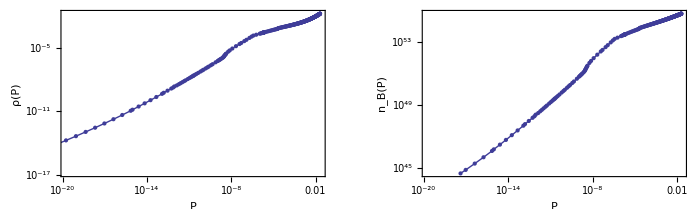

eosAPR

{0.0210736,0.01612}

0.000468294

5.03767×10^54

```mathematica
$Assumptions={η[r]≥0,η0≥0,r≥0};
SetDirectory["../EOS/"];
fileEOS={"eosAPR","eosFPS","eosAPRb","eosA","eospoly","eosMS1","eosMPA1","eosAP4","eosENG"};

fileEOS=fileEOS[[1]];
(***)
EOSv=Import[fileEOS,"Table"];

INTORD=1;
(**************third point just to be safe *********************)
EOS=Join[Table[{EOSv[[i]][[2]] cy,EOSv[[i]][[1]]cx},{i,3,Length[EOSv]}]];
EOSinv=Join[Table[{EOSv[[i]][[1]]cx,EOSv[[i]][[2]] cy},{i,3,Length[EOSv]}]];
BN=Table[{EOSv[[i]][[2]] cy,EOSv[[i]][[4]] cz},{i,3,Length[EOSv]}];
(***********************************)
ρP[x_]:=Interpolation[EOS,x,InterpolationOrder->INTORD];
Pρ[x_]:=Interpolation[EOSinv,x,InterpolationOrder->INTORD];
barnum[x_]:=Interpolation[BN,x,InterpolationOrder->INTORD];
(***********************************)
ρPT=Table[{EOS[[i]][[1]],ρP[EOS[[i]][[1]]]},{i,1,Length[EOS]}];
prho=ListLogLogPlot[{EOS},Joined->True,Frame->True,PlotRange->All,Mesh->Automatic,FrameLabel->{"P","ρ(P)"}];
pbn=ListLogLogPlot[BN,Joined->True,Frame->True,PlotRange->All,Mesh->Automatic,FrameLabel->{"P","n_B(P)"}];
GraphicsGrid[{{prho,pbn}},ImageSize->700]
x0=EOSv[[2]][[2]]cy;
(*rhoP[x_]:=Piecewise[{{Interpolation[EOS,x,InterpolationOrder->5],x>x0},{0,x<x0}}];*)

EOSin={ρ[r]->ρP[HeavisideTheta[P[r]]P[r]]};
(********************)
fileEOS
EOS[[Length[EOS]]]
ρP[10^-5]
barnum[1.1 10^-2]
```

### INTEGRATION

We first compute high-order series expansions at the center r=0 and at infinity to improve numerical stability and accuracy. The coefficients of each series are saved in a separate file, so this part has to be run only once.

#### Series at the center of the star

Zeroth and first order:

```mathematica
Clear[M,ν,P,φ0,ω1,m0,p0,v2,h2,ρ,v2h,h2h,ϕ0,ϕ2];
EQs01={E01,E02,E03,E04,E11(*,E21,E22,E26,E27,E26h,E27h,E28,E29*)};
RULEc={};
(**************)
ORD=4;
RULEc={};
(**************)
M[r_]:=Sum[Mc[i] r^i,{i,3,ORD+10}];
ν[r_]:=Sum[νc[i] r^i,{i,0,ORD+10}];
P[r_]:=Sum[Pc[i] r^i,{i,0,ORD+10}];
ρ[r_]:=rhoP[P[r]];
φ0[r_]:=Sum[φ0c[i] r^i,{i,0,ORD+10}];
(***)
ω1[r_]:=Sum[ω1c[i] r^i,{i,0,ORD+10}];
(***)

(***)
ss0=Series[EQs01//.RULEc,{r,0,ORD}];
EQc0=Union[Table[SeriesCoefficient[ss0[[1]],i]==0,{i,2,ORD}],Table[SeriesCoefficient[ss0[[2]],i]==0,{i,0,ORD}],Table[SeriesCoefficient[ss0[[3]],i]==0,{i,0,ORD}],Table[SeriesCoefficient[ss0[[4]],i]==0,{i,-1,ORD}],Table[SeriesCoefficient[ss0[[5]],i]==0,{i,-1,ORD}]];
yc0=Union[Table[Mc[i],{i,3,ORD+2}],Table[νc[i],{i,1,ORD}],Table[Pc[i],{i,1,ORD+1}],Table[φ0c[i],{i,1,ORD+2}],Table[ω1c[i],{i,1,ORD+2}]];
Length[EQc0]
Length[yc0]
systc0=Solve[EQc0,yc0][[1]]//Simplify;
Length[systc0]
Clear[M,ν,P,φ0,ω1,m0,p0,v2,h2,ρ,v2h,h2h,ϕ0,ϕ2];
```

25

25

25

Second order:

```mathematica
Clear[M,ν,P,φ0,ω1,m0,p0,v2,h2,ρ,v2h,h2h,ϕ0,ϕ2];
EQs2={E21,E22,E26,E27,E26h,E27h,E28,E29,E28h,E29h};
(**************)
ORD=4;
rulehomoscalar={};
ruleLovec={H0c[0]->0,H0c[1]->0,Φ2c[0]->0,Φ2c[1]->0,H0c[3]->0,Φ2c[3]->0,H0c[5]->0,Φ2c[5]->0,H0c[4]->-2/21 π (-6 A[φ0c[0]]^3 Φ2c[2] A'[φ0c[0]] (Pc[0] (-9+rhoP'[Pc[0]])+rhoP[Pc[0]] (-1+rhoP'[Pc[0]]))+A[φ0c[0]]^4 H0c[2] (3 Pc[0] (11+rhoP'[Pc[0]])+rhoP[Pc[0]] (1+3 rhoP'[Pc[0]]))-4 (8 H0c[2] V[φ0c[0]]+3 Φ2c[2] V'[φ0c[0]])),Φ2c[4]->1/(168 γ0)(-32 π γ0 A[φ0c[0]]^4 (3 Pc[0]-7 rhoP[Pc[0]]) Φ2c[2]+320 π γ0 V[φ0c[0]] Φ2c[2]-6 A[φ0c[0]]^2 Φ2c[2] A'[φ0c[0]]^2 (rhoP[Pc[0]] (-6+rhoP'[Pc[0]])+Pc[0] (6+rhoP'[Pc[0]]))+6 H0c[2] V'[φ0c[0]]+3 A[φ0c[0]]^3 (H0c[2] A'[φ0c[0]] (Pc[0] (-9+rhoP'[Pc[0]])+rhoP[Pc[0]] (-1+rhoP'[Pc[0]]))+2 (-3 Pc[0]+rhoP[Pc[0]]) Φ2c[2] A''[φ0c[0]])+6 Φ2c[2] V''[φ0c[0]])};
RULEc=Union[rulehomoscalar,systc0,ruleLovec,{ϕ2c[0]->0,ϕ2hc[0]->0,ϕ0c[1]->0,ϕ2c[1]->0,ϕ0hc[1]->0,ϕ2hc[1]->0,ϕ0c[2]->(ϕ0c[0] (3 A[φ0c[0]]^2 (-3 Pc[0]+rhoP[Pc[0]]) A'[φ0c[0]]^2+A[φ0c[0]]^3 (-3 Pc[0]+rhoP[Pc[0]]) A''[φ0c[0]]+V''[φ0c[0]]))/(12 γ0),ϕ0hc[2]->(ϕ0hc[0] (3 A[φ0c[0]]^2 (-3 Pc[0]+rhoP[Pc[0]]) A'[φ0c[0]]^2+A[φ0c[0]]^3 (-3 Pc[0]+rhoP[Pc[0]]) A''[φ0c[0]]+V''[φ0c[0]]))/(12 γ0),ϕ0c[3]->0,ϕ2c[3]->0,ϕ0hc[3]->0,ϕ2hc[3]->0,p0c[2]->1/(12 γ0 A[φ0c[0]]^2)ⅇ^(-νc[0]) (-96 ⅇ^νc[0] π γ0 A[φ0c[0]]^5 Pc[0] ϕ0c[0] A'[φ0c[0]]+2 ⅇ^νc[0] A[φ0c[0]]^3 (3 Pc[0]-rhoP[Pc[0]]) ϕ0c[0] A'[φ0c[0]]^3+ⅇ^νc[0] ϕ0c[0] A'[φ0c[0]]^2 V'[φ0c[0]]+4 γ0 A[φ0c[0]]^2 (ω1c[0]^2+6 ⅇ^νc[0] π ϕ0c[0] V'[φ0c[0]])+2 ⅇ^νc[0] A[φ0c[0]]^4 (3 Pc[0]-rhoP[Pc[0]]) ϕ0c[0] A'[φ0c[0]] A''[φ0c[0]]-ⅇ^νc[0] A[φ0c[0]] ϕ0c[0] (V'[φ0c[0]] A''[φ0c[0]]+A'[φ0c[0]] V''[φ0c[0]])),v2c[4]->-2/3 ⅇ^(-νc[0]) π (A[φ0c[0]]^4 (rhoP[Pc[0]] (ⅇ^νc[0] h2c[2]-ω1c[0]^2)+Pc[0] (3 ⅇ^νc[0] h2c[2]-ω1c[0]^2))-ⅇ^νc[0] A[φ0c[0]]^3 (3 Pc[0]-rhoP[Pc[0]]) ϕ2c[2] A'[φ0c[0]]+ⅇ^νc[0] (-2 h2c[2] V[φ0c[0]]+ϕ2c[2] V'[φ0c[0]])),v2hc[4]->-2/3 π (A[φ0c[0]]^4 h2hc[2] (3 Pc[0]+rhoP[Pc[0]])-2 h2hc[2] V[φ0c[0]]+A[φ0c[0]]^3 (-3 Pc[0]+rhoP[Pc[0]]) ϕ2hc[2] A'[φ0c[0]]+ϕ2hc[2] V'[φ0c[0]]),p0c[3]->0,ϕ0c[0]->0,v2c[5]->-4/3 π h2c[3] (A[φ0c[0]]^4 (3 Pc[0]+rhoP[Pc[0]])-2 V[φ0c[0]]),v2hc[5]->-4/3 π h2hc[3] (A[φ0c[0]]^4 (3 Pc[0]+rhoP[Pc[0]])-2 V[φ0c[0]]),ϕ0c[4]->(ⅇ^(-νc[0]) A[φ0c[0]]^3 (Pc[0]+rhoP[Pc[0]]) ω1c[0]^2 A'[φ0c[0]] (-3+rhoP'[Pc[0]]))/(120 γ0),ϕ2c[4]->1/(84 γ0)ⅇ^(-νc[0]) (-16 ⅇ^νc[0] π γ0 A[φ0c[0]]^4 (3 Pc[0]-7 rhoP[Pc[0]]) ϕ2c[2]-3 ⅇ^νc[0] A[φ0c[0]]^2 ϕ2c[2] A'[φ0c[0]]^2 (rhoP[Pc[0]] (-6+rhoP'[Pc[0]])+Pc[0] (6+rhoP'[Pc[0]]))-A[φ0c[0]]^3 (A'[φ0c[0]] (rhoP[Pc[0]] (-3 (ⅇ^νc[0] h2c[2]+ω1c[0]^2)+(3 ⅇ^νc[0] h2c[2]+ω1c[0]^2) rhoP'[Pc[0]])+Pc[0] (-3 (9 ⅇ^νc[0] h2c[2]+ω1c[0]^2)+(3 ⅇ^νc[0] h2c[2]+ω1c[0]^2) rhoP'[Pc[0]]))+3 ⅇ^νc[0] (3 Pc[0]-rhoP[Pc[0]]) ϕ2c[2] A''[φ0c[0]])+ⅇ^νc[0] (160 π γ0 V[φ0c[0]] ϕ2c[2]-6 h2c[2] V'[φ0c[0]]+3 ϕ2c[2] V''[φ0c[0]])),ϕ0hc[4]->1/(1440 γ0^2)ϕ0hc[0] (-9 A[φ0c[0]] A'[φ0c[0]]^3 (rhoP[Pc[0]] (-5+rhoP'[Pc[0]])+Pc[0] (3+rhoP'[Pc[0]])) V'[φ0c[0]]+96 π γ0 V'[φ0c[0]]^2+3 A[φ0c[0]]^5 (3 Pc[0]-rhoP[Pc[0]]) A'[φ0c[0]]^2 (rhoP[Pc[0]] (-18+rhoP'[Pc[0]])+Pc[0] (42+rhoP'[Pc[0]])) A''[φ0c[0]]-8 π γ0 A[φ0c[0]]^7 (9 Pc[0]^2 (-5+rhoP'[Pc[0]])+12 Pc[0] rhoP[Pc[0]] (1+rhoP'[Pc[0]])+rhoP[Pc[0]]^2 (-23+3 rhoP'[Pc[0]])) A''[φ0c[0]]+V''[φ0c[0]] (160 π γ0 V[φ0c[0]]+3 V''[φ0c[0]])+A[φ0c[0]]^4 (9 (3 Pc[0]-rhoP[Pc[0]]) A'[φ0c[0]]^4 (rhoP[Pc[0]] (-8+rhoP'[Pc[0]])+Pc[0] (12+rhoP'[Pc[0]]))+16 π γ0 (-3 Pc[0]+7 rhoP[Pc[0]]) V''[φ0c[0]])+3 A[φ0c[0]]^2 A'[φ0c[0]] (16 π γ0 V[φ0c[0]] A'[φ0c[0]] (3 Pc[0] (-13+rhoP'[Pc[0]])+rhoP[Pc[0]] (1+3 rhoP'[Pc[0]]))-(rhoP[Pc[0]] (-12+rhoP'[Pc[0]])+Pc[0] (24+rhoP'[Pc[0]])) V'[φ0c[0]] A''[φ0c[0]]+6 (-3 Pc[0]+rhoP[Pc[0]]) A'[φ0c[0]] V''[φ0c[0]])-3 A[φ0c[0]]^6 (8 π γ0 A'[φ0c[0]]^2 (rhoP[Pc[0]]^2 (-31+3 rhoP'[Pc[0]])+3 Pc[0]^2 (-23+3 rhoP'[Pc[0]])+4 Pc[0] rhoP[Pc[0]] (11+3 rhoP'[Pc[0]]))-(-3 Pc[0]+rhoP[Pc[0]])^2 A''[φ0c[0]]^2-(-3 Pc[0]+rhoP[Pc[0]])^2 A'[φ0c[0]] Derivative[3][A][φ0c[0]])+3 V'[φ0c[0]] Derivative[3][V][φ0c[0]]+A[φ0c[0]]^3 (16 π γ0 V[φ0c[0]] (3 Pc[0] (-13+rhoP'[Pc[0]])+rhoP[Pc[0]] (1+3 rhoP'[Pc[0]])) A''[φ0c[0]]-3 (3 Pc[0]-rhoP[Pc[0]]) (2 A''[φ0c[0]] V''[φ0c[0]]+V'[φ0c[0]] Derivative[3][A][φ0c[0]])+A'[φ0c[0]] (-96 π γ0 (5 Pc[0]-3 rhoP[Pc[0]]) V'[φ0c[0]]+3 (-3 Pc[0]+rhoP[Pc[0]]) Derivative[3][V][φ0c[0]]))),ϕ2hc[4]->-1/(84 γ0)(16 π γ0 A[φ0c[0]]^4 (3 Pc[0]-7 rhoP[Pc[0]]) ϕ2hc[2]-160 π γ0 V[φ0c[0]] ϕ2hc[2]+3 A[φ0c[0]]^2 ϕ2hc[2] A'[φ0c[0]]^2 (rhoP[Pc[0]] (-6+rhoP'[Pc[0]])+Pc[0] (6+rhoP'[Pc[0]]))+6 h2hc[2] V'[φ0c[0]]+3 A[φ0c[0]]^3 (h2hc[2] A'[φ0c[0]] (Pc[0] (-9+rhoP'[Pc[0]])+rhoP[Pc[0]] (-1+rhoP'[Pc[0]]))+(3 Pc[0]-rhoP[Pc[0]]) ϕ2hc[2] A''[φ0c[0]])-3 ϕ2hc[2] V''[φ0c[0]]),m0c[5]->1/(90 γ0)ⅇ^(-νc[0]) (-8 π γ0 A[φ0c[0]]^4 (27 Pc[0]-13 rhoP[Pc[0]]) ω1c[0]^2-40 γ0 (9 ⅇ^νc[0] p0c[4]-8 π V[φ0c[0]] ω1c[0]^2)-3 A[φ0c[0]]^2 (Pc[0]+rhoP[Pc[0]]) ω1c[0]^2 A'[φ0c[0]]^2 (-3+rhoP'[Pc[0]])),p0c[4]->-1/(360 γ0)ⅇ^(-νc[0]) ω1c[0]^2 (-320 π γ0 V[φ0c[0]]+3 A[φ0c[0]]^2 (Pc[0]+rhoP[Pc[0]]) A'[φ0c[0]]^2 (-3+rhoP'[Pc[0]])+8 π γ0 A[φ0c[0]]^4 (3 Pc[0] (11+rhoP'[Pc[0]])+rhoP[Pc[0]] (-7+3 rhoP'[Pc[0]])))}];
(**************)
M[r_]:=Sum[Mc[i] r^i,{i,3,ORD+10}];
λ[r_]:=-Log[1-2M[r]/r];
ν[r_]:=Sum[νc[i] r^i,{i,0,ORD+10}];
P[r_]:=Sum[Pc[i] r^i,{i,0,ORD+10}];
ρ[r_]:=rhoP[P[r]];
φ0[r_]:=Sum[φ0c[i] r^i,{i,0,ORD+10}];
(***)
ω1[r_]:=Sum[ω1c[i] r^i,{i,0,ORD+10}];
(***)
m0[r_]:=Sum[m0c[i] r^i,{i,5,ORD+10}];
p0[r_]:=Sum[p0c[i] r^i,{i,2,ORD+10}];
v2[r_]:=Sum[v2c[i] r^i,{i,4,ORD+10}];
h2[r_]:=Sum[h2c[i] r^i,{i,2,ORD+10}];
v2h[r_]:=Sum[v2hc[i] r^i,{i,4,ORD+10}];
h2h[r_]:=Sum[h2hc[i] r^i,{i,2,ORD+10}];
ϕ0[r_]:=Sum[ϕ0c[i] r^i,{i,0,ORD+10}];
ϕ2[r_]:=Sum[ϕ2c[i] r^i,{i,0,ORD+10}];
ϕ0h[r_]:=Sum[ϕ0hc[i] r^i,{i,0,ORD+10}];
ϕ2h[r_]:=Sum[ϕ2hc[i] r^i,{i,0,ORD+10}];
(***)
H0[r_]:=Sum[H0c[i] r^i,{i,0,ORD+10}];
Φ2[r_]:=Sum[Φ2c[i] r^i,{i,0,ORD+10}];
(***)
Timing[ss2=Series[{eqLove1,eqLove2}/.dPdρ->1/rhoP'[P[r]](*Drop[EQs2,-4]*)//.RULEc,{r,0,ORD-1}]]//Simplify
(*EQc2=Union[Table[SeriesCoefficient[ss0[[1]],i]==0,{i,2,ORD}],Table[SeriesCoefficient[ss0[[2]],i]==0,{i,0,ORD}],Table[SeriesCoefficient[ss0[[3]],i]==0,{i,0,ORD}],Table[SeriesCoefficient[ss0[[4]],i]==0,{i,-1,ORD}],Table[SeriesCoefficient[ss0[[5]],i]==0,{i,-1,ORD}]];
yc2=Union[Table[Mc[i],{i,3,ORD+2}],Table[νc[i],{i,1,ORD}],Table[Pc[i],{i,1,ORD+1}],Table[φ0c[i],{i,1,ORD+2}],Table[ω1c[i],{i,1,ORD+2}]];
Length[EQc2]
Length[yc2]*)
(*systc2=Solve[EQc2,yc2][[1]]//Simplify;
Length[systc2]*)
Clear[M,ν,P,φ0,ω1,m0,p0,v2,h2,ρ,v2h,h2h,ϕ0,ϕ2,ϕ0h,ϕ2h,H0,Φ2];
```

{0.37,{O[r]^4,O[r]^4}}

```mathematica
Solve[{14 H0c[4]-128/3 π H0c[2] V[φ0c[0]]-8 π A[φ0c[0]]^3 Φ2c[2] A'[φ0c[0]] (Pc[0] (-9+rhoP'[Pc[0]])+rhoP[Pc[0]] (-1+rhoP'[Pc[0]]))+4/3 π A[φ0c[0]]^4 H0c[2] (3 Pc[0] (11+rhoP'[Pc[0]])+rhoP[Pc[0]] (1+3 rhoP'[Pc[0]]))-16 π Φ2c[2] V'[φ0c[0]]==0,1/(12 γ0)(32 π γ0 A[φ0c[0]]^4 (3 Pc[0]-7 rhoP[Pc[0]]) Φ2c[2]+6 A[φ0c[0]]^2 Φ2c[2] A'[φ0c[0]]^2 (rhoP[Pc[0]] (-6+rhoP'[Pc[0]])+Pc[0] (6+rhoP'[Pc[0]]))-3 A[φ0c[0]]^3 (H0c[2] A'[φ0c[0]] (Pc[0] (-9+rhoP'[Pc[0]])+rhoP[Pc[0]] (-1+rhoP'[Pc[0]]))+2 (-3 Pc[0]+rhoP[Pc[0]]) Φ2c[2] A''[φ0c[0]])-2 (160 π γ0 V[φ0c[0]] Φ2c[2]-84 γ0 Φ2c[4]+3 H0c[2] V'[φ0c[0]]+3 Φ2c[2] V''[φ0c[0]])) r^2==0},{H0c[4],Φ2c[4]}]//Simplify
```

{{H0c[4]→-2/21 π (-6 A[φ0c[0]]^3 Φ2c[2] A'[φ0c[0]] (Pc[0] (-9+rhoP'[Pc[0]])+rhoP[Pc[0]] (-1+rhoP'[Pc[0]]))+A[φ0c[0]]^4 H0c[2] (3 Pc[0] (11+rhoP'[Pc[0]])+rhoP[Pc[0]] (1+3 rhoP'[Pc[0]]))-4 (8 H0c[2] V[φ0c[0]]+3 Φ2c[2] V'[φ0c[0]])),Φ2c[4]→1/(168 γ0)(-32 π γ0 A[φ0c[0]]^4 (3 Pc[0]-7 rhoP[Pc[0]]) Φ2c[2]+320 π γ0 V[φ0c[0]] Φ2c[2]-6 A[φ0c[0]]^2 Φ2c[2] A'[φ0c[0]]^2 (rhoP[Pc[0]] (-6+rhoP'[Pc[0]])+Pc[0] (6+rhoP'[Pc[0]]))+6 H0c[2] V'[φ0c[0]]+3 A[φ0c[0]]^3 (H0c[2] A'[φ0c[0]] (Pc[0] (-9+rhoP'[Pc[0]])+rhoP[Pc[0]] (-1+rhoP'[Pc[0]]))+2 (-3 Pc[0]+rhoP[Pc[0]]) Φ2c[2] A''[φ0c[0]])+6 Φ2c[2] V''[φ0c[0]])}}

```mathematica
EQc2=Union[Table[SeriesCoefficient[ss2[[1]],i]==0,{i,0,ORD}],Table[SeriesCoefficient[ss2[[2]],i]==0,{i,2,ORD}],Table[SeriesCoefficient[ss2[[3]],i]==0,{i,2,ORD}],Table[SeriesCoefficient[ss2[[4]],i]==0,{i,-1,ORD}],Table[SeriesCoefficient[ss2[[5]],i]==0,{i,1,ORD}],Table[SeriesCoefficient[ss2[[6]],i]==0,{i,-1,ORD}],Table[SeriesCoefficient[ss2[[7]],i]==0,{i,-1,ORD}],Table[SeriesCoefficient[ss2[[8]],i]==0,{i,-2,ORD}],Table[SeriesCoefficient[ss2[[9]],i]==0,{i,-1,ORD}],Table[SeriesCoefficient[ss2[[10]],i]==0,{i,-2,ORD}]];
yc2=Union[Table[Mc[i],{i,3,ORD+2}],Table[νc[i],{i,1,ORD}],Table[Pc[i],{i,1,ORD+1}],Table[φ0c[i],{i,1,ORD+2}],Table[ω1c[i],{i,1,ORD+2}]];
Length[EQc2]
Length[yc2]
(*systc2=Solve[EQc2,yc2][[1]]//Simplify;
Length[systc2]*)
```

Part::partw: Part 3 of (m0c[6] + 5 p0c[5] + 5 ϕ0c[5] SuperscriptBox[O[r]^5 does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

47

25

```mathematica
Solve[12 γ0 ϕ0hc[2]+3 A[φ0c[0]]^2 (3 Pc[0]-rhoP[Pc[0]]) ϕ0hc[0] A'[φ0c[0]]^2+A[φ0c[0]]^3 (3 Pc[0]-rhoP[Pc[0]]) ϕ0hc[0] A''[φ0c[0]]-ϕ0hc[0] V''[φ0c[0]]==0,ϕ0hc[2]]//FullSimplify
```

{{ϕ0hc[2]→(ϕ0hc[0] (-A[φ0c[0]]^2 (3 Pc[0]-rhoP[Pc[0]]) (3 A'[φ0c[0]]^2+A[φ0c[0]] A''[φ0c[0]])+V''[φ0c[0]]))/(12 γ0)}}

```mathematica
(******************)
(*Series[{EQs[[9]]}//.systc0,{r,0,4}]//Simplify
Series[{EQs[[10]]}//.systc0,{r,0,4}]//Simplify*)
ruleC=Union[RULEc,{νc[0]->1,Pc[0]->10^-4,φ0c[0]->0.1,ω1c[0]->1,h2c[2]->1.12,h2hc[2]->1.15,γ0->1/2}];
V[x_]:=x^2;
A[x_]:=Exp[x];
rhoP[x_]:=ρP[x];
Sum[Mc[i] r^i,{i,3,5}]//.ruleC//N
Sum[νc[i] r^i,{i,0,4}]//.ruleC//N
Sum[Pc[i] r^i,{i,0,4}]//.ruleC//N
Sum[φ0c[i] r^i,{i,0,4}]//.ruleC//N
Sum[ω1c[i] r^i,{i,0,4}]//.ruleC//N
Sum[m0c[i] r^i,{i,5,5}]//.ruleC//N
Sum[p0c[i] r^i,{i,2,2}]//.ruleC//N
Sum[v2c[i] r^i,{i,4,4}]//.ruleC//N
Sum[h2c[i] r^i,{i,2,2}]//.ruleC//N
Sum[v2hc[i] r^i,{i,4,4}]//.ruleC//N
Sum[h2hc[i] r^i,{i,2,2}]//.ruleC//N
Sum[ϕ0c[i] r^i,{i,0,4}]//.ruleC//N
Sum[ϕ2c[i] r^i,{i,0,4}]//.ruleC//N
Sum[ϕ0hc[i] r^i,{i,0,4}]//.ruleC//N
Sum[ϕ2hc[i] r^i,{i,0,4}]//.ruleC//N
Clear[A,V,rhoP]

(*Clear[M,ν,P,φ0,ω1,m0,p0,v2,h2,ρ,v2h,h2h,ϕ0,ϕ2];*)
```

0.0496813 r^3+0.0232465 r^5

1.-0.0741077 r^2-0.0199119 r^4

0.0001+4.69487×10^-6 r^2+6.78967×10^-6 r^4

0.1+0.0335688 r^2+0.00494989 r^4

1.+0.010102 r^2+0.000967934 r^4

0.0040842 r^5

0.122626 r^2

-0.770485 r^4 (0.00501719+2.71828 (-0.0224+0.2 ϕ2c[2.])+0.00384091 ϕ2c[2.])

1.12 r^2

-2.0944 r^4 (-0.0203457+0.201413 ϕ2hc[2.])

1.15 r^2

0.+0.0000196412 r^4

r^2 ϕ2c[2.]+0.00875903 r^4 (-1.34986 (0.0431694-0.00853625 ϕ2c[2.])+0.867626 ϕ2c[2.]+2.71828 (-1.344+8.51327 ϕ2c[2.]))

ϕ0hc[0.]+0.334275 r^2 ϕ0hc[0.]+0.0664875 r^4 ϕ0hc[0.]

-0.0238095 r^4 (1.38+4.04958 (0.0051367-0.00104677 ϕ2hc[2.])-8.83246 ϕ2hc[2.])+r^2 ϕ2hc[2.]

```mathematica
SetDirectory[NotebookDirectory[]];
DumpSave["series_center_ST.mx",{RULEc,ORD}];
```

```mathematica
Quit[];
```

#### Series infinity. This is specialized for V=0

Zeroth and first order:

```mathematica
Clear[M,ν,P,φ0,ω1,m0,p0,v2,h2,ρ,v2h,h2h,ϕ0,ϕ2];
EQs01={E01,E02,E03,E04,E11(*,E21,E22,E26,E27,E26h,E27h,E28,E29*)};
(**************)
ORD=7;
RULEc0={};
(**************)
V[x_]:=0;
(**************)
M[r_]:=Sum[Mc[i] r^-i,{i,0,ORD+10}];
ν[r_]:=Sum[νc[i] r^-i,{i,0,ORD+10}];
P[r_]:=0;
ρ[r_]:=0;
φ0[r_]:=Sum[φ0c[i] r^-i,{i,0,ORD+10}];
(***)
ω1[r_]:=Sum[ω1c[i] r^-i,{i,0,ORD+10}];
(***)
			
(***)
ss0=Series[EQs01//.RULEc0,{r,∞,ORD+1}];

EQc0=Union[Table[SeriesCoefficient[ss0[[1]],i]==0,{i,2,ORD}],Table[SeriesCoefficient[ss0[[2]],i]==0,{i,2,ORD}],Table[SeriesCoefficient[ss0[[4]],i]==0,{i,4,ORD+1}],Table[SeriesCoefficient[ss0[[5]],i]==0,{i,3,ORD+1}]];
yc0=Union[Table[Mc[i],{i,1,ORD-1}],Table[νc[i],{i,1,ORD-1}],Table[φ0c[i],{i,2,ORD-1}],Table[ω1c[i],{i,1,ORD-1}]];
Length[EQc0]
Length[yc0]
systc0=Solve[EQc0,yc0][[1]]//Simplify
Length[systc0]
Clear[M,ν,P,φ0,ω1,m0,p0,v2,h2,ρ,v2h,h2h,ϕ0,ϕ2,V];
```

23

23

Solve::svars: Equations may not give solutions for all "solve" variables.

{Mc[1]→-4 π γ0 φ0c[1]^2,Mc[2]→-4 π γ0 Mc[0] φ0c[1]^2,Mc[3]→-16/3 π γ0 Mc[0]^2 φ0c[1]^2,Mc[4]→8/3 π γ0 Mc[0] φ0c[1]^2 (-3 Mc[0]^2+π γ0 φ0c[1]^2),Mc[5]→64/5 π γ0 Mc[0]^2 φ0c[1]^2 (-Mc[0]^2+π γ0 φ0c[1]^2),Mc[6]→-32/45 π γ0 Mc[0] φ0c[1]^2 (30 Mc[0]^4-59 π γ0 Mc[0]^2 φ0c[1]^2+9 π^2 γ0^2 φ0c[1]^4),νc[1]→-2 Mc[0],νc[2]→-2 Mc[0]^2,νc[3]→8/3 (-Mc[0]^3+π γ0 Mc[0] φ0c[1]^2),νc[4]→-4 Mc[0]^4+32/3 π γ0 Mc[0]^2 φ0c[1]^2,νc[5]→-16/15 (6 Mc[0]^5-29 π γ0 Mc[0]^3 φ0c[1]^2+9 π^2 γ0^2 Mc[0] φ0c[1]^4),νc[6]→-32/15 (5 Mc[0]^6-37 π γ0 Mc[0]^4 φ0c[1]^2+32 π^2 γ0^2 Mc[0]^2 φ0c[1]^4),φ0c[2]→Mc[0] φ0c[1],φ0c[3]→-4/3 (-Mc[0]^2 φ0c[1]+π γ0 φ0c[1]^3),φ0c[4]→2 Mc[0]^3 φ0c[1]-16/3 π γ0 Mc[0] φ0c[1]^3,φ0c[5]→8/15 (6 Mc[0]^4 φ0c[1]-29 π γ0 Mc[0]^2 φ0c[1]^3+9 π^2 γ0^2 φ0c[1]^5),φ0c[6]→16/15 (5 Mc[0]^5 φ0c[1]-37 π γ0 Mc[0]^3 φ0c[1]^3+32 π^2 γ0^2 Mc[0] φ0c[1]^5),ω1c[1]→0,ω1c[2]→0,ω1c[4]→0,ω1c[5]→-12/5 π γ0 φ0c[1]^2 ω1c[3],ω1c[6]→-16/3 π γ0 Mc[0] φ0c[1]^2 ω1c[3]}

22

Second order:

```mathematica
Clear[M,ν,P,φ0,ω1,m0,p0,v2,h2,ρ,v2h,h2h,ϕ0,ϕ2];
(**************)
V[x_]:=0;
P[r_]:=0;
ρ[r_]:=0;
p0[r_]:=0;
(**************)
eqLove10=eqLove1//Simplify;
eqLove20=eqLove2//Simplify;
EQs2={E22,E26,E27,E26h,E27h,E28,E29,E28h,E29h}//Simplify;
```

```mathematica
(**************)
ORD=5;
rulehomoscalar={};
ruleparam={Mc[0]->MASS,νc[0]->0,ω1c[0]->Ω,ω1c[3]->-2J,φ0c[0]->0,m0c[0]->δM};
ruleLoveINF={Φ2c[-1]->-2 MASS Φ2c[-2],H0c[-1]->-2 MASS H0c[-2],H0c[0]->16/3 π γ0 φ0c[1] (H0c[-2] φ0c[1]-2 MASS Φ2c[-2]),Φ2c[0]->1/3 MASS (-H0c[-2] φ0c[1]+2 MASS Φ2c[-2]),H0c[1]->8/3 MASS π γ0 H0c[-2] φ0c[1]^2,Φ2c[1]->8/3 MASS π γ0 φ0c[1]^2 Φ2c[-2],H0c[2]->16/3 MASS^2 π γ0 H0c[-2] φ0c[1]^2,Φ2c[2]->16/3 MASS^2 π γ0 φ0c[1]^2 Φ2c[-2],H0c[4]->-1/45 MASS (-135 H0c[3]+16 MASS π γ0 H0c[-2] φ0c[1]^2 (33 MASS^2+47 π γ0 φ0c[1]^2)),Φ2c[4]->-1/45 MASS (528 MASS^3 π γ0 φ0c[1]^2 Φ2c[-2]+752 MASS π^2 γ0^2 φ0c[1]^4 Φ2c[-2]-135 Φ2c[3]),H0c[5]->-2/315 (6000 MASS^5 π γ0 H0c[-2] φ0c[1]^2+810 π γ0 H0c[3] φ0c[1]^2+4624 MASS^3 π^2 γ0^2 H0c[-2] φ0c[1]^4+6912 MASS^4 π^2 γ0^2 φ0c[1]^3 Φ2c[-2]-9 MASS^2 (125 H0c[3]+768 π^3 γ0^3 φ0c[1]^5 Φ2c[-2])+144 MASS (4 π^3 γ0^3 H0c[-2] φ0c[1]^6-5 π γ0 φ0c[1] Φ2c[3])),Φ2c[5]->1/315 (-432 MASS^4 π γ0 H0c[-2] φ0c[1]^3-11136 MASS^5 π γ0 φ0c[1]^2 Φ2c[-2]-17024 MASS^3 π^2 γ0^2 φ0c[1]^4 Φ2c[-2]+45 MASS φ0c[1] (H0c[3]+128 π^3 γ0^3 φ0c[1]^5 Φ2c[-2])-900 π γ0 φ0c[1]^2 Φ2c[3]+432 MASS^2 (π^2 γ0^2 H0c[-2] φ0c[1]^5+5 Φ2c[3])),H0c[6]->1/945 (315 H0c[-2] Mc[7]-79200 MASS^6 π γ0 H0c[-2] φ0c[1]^2-8352 MASS^4 π^2 γ0^2 H0c[-2] φ0c[1]^4-161280 MASS^7 π γ0 φ0c[1] Φ2c[-2]+1453824 MASS^5 π^2 γ0^2 φ0c[1]^3 Φ2c[-2]+2 MASS^3 (7425 H0c[3]-1242112 π^3 γ0^3 φ0c[1]^5 Φ2c[-2])+360 MASS π γ0 (-78 H0c[3] φ0c[1]^2+7 (160 π^3 γ0^3 φ0c[1]^7+7 φ0c[7]) Φ2c[-2])+32 MASS^2 (2456 π^3 γ0^3 H0c[-2] φ0c[1]^6+675 π γ0 φ0c[1] Φ2c[3])),Φ2c[6]->-16/3 MASS^7 H0c[-2] φ0c[1]+5048/105 MASS^5 π γ0 H0c[-2] φ0c[1]^3-5056/21 MASS^6 π γ0 φ0c[1]^2 Φ2c[-2]+8128/5 MASS^4 π^2 γ0^2 φ0c[1]^4 Φ2c[-2]+1/3 (Mc[7]+1280 π^4 γ0^4 φ0c[1]^8+56 π γ0 φ0c[1] φ0c[7]) Φ2c[-2]+MASS^2 (5/7 H0c[3] φ0c[1]-2509312/945 π^3 γ0^3 φ0c[1]^6 Φ2c[-2])+MASS^3 (-77632/945 π^2 γ0^2 H0c[-2] φ0c[1]^5+(100 Φ2c[3])/7)+MASS (40/3 π^3 γ0^3 H0c[-2] φ0c[1]^7+7/12 H0c[-2] φ0c[7]-128/7 π γ0 φ0c[1]^2 Φ2c[3])};
RULEINF=Union[rulehomoscalar,systc0,ruleparam,ruleLoveINF,{}];
(**************)
M[r_]:=Sum[Mc[i] r^-i,{i,0,ORD+2}];
λ[r_]:=-Log[1-2M[r]/r];
ν[r_]:=Sum[νc[i] r^-i,{i,0,ORD+2}];

φ0[r_]:=Sum[φ0c[i] r^-i,{i,0,ORD+2}];
(***)
ω1[r_]:=Sum[ω1c[i] r^-i,{i,0,ORD+2}];
(***)
m0[r_]:=Sum[m0c[i] r^-i,{i,0,ORD+2}];
(*p0[r_]:=Sum[p0c[i] r^-i,{i,0,ORD+6}];*)
v2[r_]:=Sum[v2c[i] r^-i,{i,-2,ORD+2}];
h2[r_]:=Sum[h2c[i] r^-i,{i,-2,ORD+2}];
v2h[r_]:=Sum[v2hc[i] r^-i,{i,-2,ORD+2}];
h2h[r_]:=Sum[h2hc[i] r^-i,{i,-2,ORD+2}];
ϕ0[r_]:=Sum[ϕ0c[i] r^-i,{i,-2,ORD+2}];
ϕ2[r_]:=Sum[ϕ2c[i] r^-i,{i,-2,ORD+2}];
ϕ0h[r_]:=Sum[ϕ0hc[i] r^-i,{i,-2,ORD+2}];
ϕ2h[r_]:=Sum[ϕ2hc[i] r^-i,{i,-2,ORD+2}];
(***)
H0[r_]:=Sum[H0c[i] r^-i,{i,-2,ORD+2}];
Φ2[r_]:=Sum[Φ2c[i] r^-i,{i,-2,ORD+2}];
(***)
Timing[ss2=Series[EQs2(*Drop[EQs2,0]*)//.RULEINF,{r,∞,ORD+2}]]//Simplify;
EQc2=Union[Table[SeriesCoefficient[ss2[[1]],i]==0,{i,-1,ORD}],Table[SeriesCoefficient[ss2[[2]],i]==0,{i,-1,ORD}],Table[SeriesCoefficient[ss2[[3]],i]==0,{i,-2,ORD}],Table[SeriesCoefficient[ss2[[4]],i]==0,{i,-1,ORD}],Table[SeriesCoefficient[ss2[[5]],i]==0,{i,-2,ORD}],Table[SeriesCoefficient[ss2[[6]],i]==0,{i,0,ORD}],Table[SeriesCoefficient[ss2[[7]],i]==0,{i,1,ORD+2}],Table[SeriesCoefficient[ss2[[8]],i]==0,{i,0,ORD}],Table[SeriesCoefficient[ss2[[9]],i]==0,{i,-1,ORD+2}]];
yc2=Union[Table[m0c[i],{i,0,ORD-1}],Table[v2c[i],{i,-2,ORD}],Table[h2c[i],{i,-1,ORD-1}],Table[v2hc[i],{i,-2,ORD}],Table[h2hc[i],{i,-1,ORD-1}],Table[ϕ0c[i],{i,-2,ORD-1}],Table[ϕ2c[i],{i,-1,ORD-1}],Table[ϕ0hc[i],{i,-2,ORD-2}],Table[ϕ2hc[i],{i,-2,ORD-1}]];
Length[EQc2]
Length[yc2]
systc2=Solve[EQc2,yc2][[1]]//Simplify;
Length[systc2]

Series[{eqLove10,eqLove20}//.RULEINF,{r,∞,8}]//Simplify
Series[{H0[r],Φ2[r]}//.RULEINF,{r,∞,5}]//Simplify
Clear[M,ν,P,φ0,ω1,m0,p0,v2,h2,ρ,v2h,h2h,ϕ0,ϕ2,ϕ0h,ϕ2h,V,λ,H0,Φ2];
```

64

59

Solve::svars: Equations may not give solutions for all "solve" variables.

48

{O[1/r]^9,O[1/r]^9}

{H0c[-2] r^2-2 (MASS H0c[-2]) r+16/3 π γ0 φ0c[1] (H0c[-2] φ0c[1]-2 MASS Φ2c[-2])+(8 MASS π γ0 H0c[-2] φ0c[1]^2)/(3 r)+(16 MASS^2 π γ0 H0c[-2] φ0c[1]^2)/(3 r^2)+H0c[3]/r^3-(MASS (-135 H0c[3]+16 MASS π γ0 H0c[-2] φ0c[1]^2 (33 MASS^2+47 π γ0 φ0c[1]^2)))/(45 r^4)-1/(315 r^5)2 (6000 MASS^5 π γ0 H0c[-2] φ0c[1]^2+810 π γ0 H0c[3] φ0c[1]^2+4624 MASS^3 π^2 γ0^2 H0c[-2] φ0c[1]^4+6912 MASS^4 π^2 γ0^2 φ0c[1]^3 Φ2c[-2]-9 MASS^2 (125 H0c[3]+768 π^3 γ0^3 φ0c[1]^5 Φ2c[-2])+144 MASS (4 π^3 γ0^3 H0c[-2] φ0c[1]^6-5 π γ0 φ0c[1] Φ2c[3]))+O[1/r]^6,Φ2c[-2] r^2-2 (MASS Φ2c[-2]) r+1/3 MASS (-H0c[-2] φ0c[1]+2 MASS Φ2c[-2])+(8 MASS π γ0 φ0c[1]^2 Φ2c[-2])/(3 r)+(16 MASS^2 π γ0 φ0c[1]^2 Φ2c[-2])/(3 r^2)+Φ2c[3]/r^3-(MASS (528 MASS^3 π γ0 φ0c[1]^2 Φ2c[-2]+752 MASS π^2 γ0^2 φ0c[1]^4 Φ2c[-2]-135 Φ2c[3]))/(45 r^4)+1/(315 r^5)(-432 MASS^4 π γ0 H0c[-2] φ0c[1]^3-11136 MASS^5 π γ0 φ0c[1]^2 Φ2c[-2]-17024 MASS^3 π^2 γ0^2 φ0c[1]^4 Φ2c[-2]+45 MASS φ0c[1] (H0c[3]+128 π^3 γ0^3 φ0c[1]^5 Φ2c[-2])-900 π γ0 φ0c[1]^2 Φ2c[3]+432 MASS^2 (π^2 γ0^2 H0c[-2] φ0c[1]^5+5 Φ2c[3]))+O[1/r]^6}

```mathematica
(******************)
(*Series[{EQs[[9]]}//.systc0,{r,0,4}]//Simplify
Series[{EQs[[10]]}//.systc0,{r,0,4}]//Simplify*)
ruleC=Union[systc0,systc2(*,{νc[0]->1,Pc[0]->10^-4,φ0c[0]->0.1,ω1c[0]->1,h2c[2]->1,h2hc[2]->1,γ0->1/2}*)];
(*V[x_]:=0;
A[x_]:=Exp[x];
rhoP[x_]:=ρP[x];
Clear[rhoP,A,V];*)
SSS[X_]:=Series[Sum[X r^-i,{i,-2,3}]//.ruleC,{r,∞,3}];
(*SSS[Mc[i]]
SSS[νc[i]]
SSS[Pc[i]]
SSS[φ0c[i]]
SSS[ω1c[i]]
SSS[m0c[i]]*)
(*SSS[p0c[i]]*)
(*SSS[v2c[i]]
SSS[h2c[i]]
SSS[v2hc[i]]
SSS[h2hc[i]]
SSS[ϕ0c[i]]

SSS[ϕ0hc[i]]
SSS[ϕ2hc[i]]*)
SSS[ϕ2c[i]];
SSS[h2c[i]];
SSS[h2hc[i]];
(*love=Series[(1-gtt)/2//.ruleC/.{Mc[0]->MASS,νc[0]->0,h0[r]->0,J->0},{r,∞,3}]//FullSimplify*)
Clear[A,V,rhoP]

(*Clear[M,ν,P,φ0,ω1,m0,p0,v2,h2,ρ,v2h,h2h,ϕ0,ϕ2];*)
```

h2c[-2] P2[θ] r^2-4 (MASS h2c[-2] P2[θ]) r+(1+4/3 P2[θ] (h2c[-2] (3 MASS^2+4 π γ0 φ0c[1]^2)+4 MASS π γ0 φ0c[1] ϕ2c[-2]))-(MASS (3+16 π γ0 P2[θ] φ0c[1] (h2c[-2] φ0c[1]+2 MASS ϕ2c[-2])))/(3 r)+1/(90 MASS φ0c[1] r^3)(8 MASS π γ0 φ0c[1]^2 (MASS φ0c[1] (15-8 h2c[-2] P2[θ] (3 MASS^2+7 π γ0 φ0c[1]^2))-48 P2[θ] (29 MASS^4+41 MASS^2 π γ0 φ0c[1]^2-15 π^2 γ0^2 φ0c[1]^4) ϕ2c[-2])+180 P2[θ] (12 MASS^2-5 π γ0 φ0c[1]^2) ϕ2c[3]-315 P2[θ] ϕ2c[5])+O[1/r]^4

```mathematica
SetDirectory[NotebookDirectory[]];
DumpSave["series_inf_ST.mx",{RULEINF,ORD}];
```

```mathematica
Quit[];
```

#### Asymptotic behavior of the equations for the tidal deformation

Here we use the asymptotic behavior of H0 and Φ2 to build a suitable linear combination that satisfied the correct boundary conditions at infinity. The results of this computation are then used in the integrator below.

```mathematica
H0inf=H0c[-2] r^2-2 (MASS H0c[-2]) r+16/3 π γ0 φ0c[1] (H0c[-2] φ0c[1]-2 MASS Φ2c[-2])+(8 MASS π γ0 H0c[-2] φ0c[1]^2)/(3 r)+(16 MASS^2 π γ0 H0c[-2] φ0c[1]^2)/(3 r^2)+H0c[3]/r^3-1/(45 r^4)MASS (-135 H0c[3]+16 MASS π γ0 H0c[-2] φ0c[1]^2 (33 MASS^2+47 π γ0 φ0c[1]^2))-1/(315 r^5)2 (6000 MASS^5 π γ0 H0c[-2] φ0c[1]^2+810 π γ0 H0c[3] φ0c[1]^2+4624 MASS^3 π^2 γ0^2 H0c[-2] φ0c[1]^4+6912 MASS^4 π^2 γ0^2 φ0c[1]^3 Φ2c[-2]-9 MASS^2 (125 H0c[3]+768 π^3 γ0^3 φ0c[1]^5 Φ2c[-2])+144 MASS (4 π^3 γ0^3 H0c[-2] φ0c[1]^6-5 π γ0 φ0c[1] Φ2c[3]));

Φ2inf=Φ2c[-2] r^2-2 (MASS Φ2c[-2]) r+1/3 MASS (-H0c[-2] φ0c[1]+2 MASS Φ2c[-2])+(8 MASS π γ0 φ0c[1]^2 Φ2c[-2])/(3 r)+(16 MASS^2 π γ0 φ0c[1]^2 Φ2c[-2])/(3 r^2)+Φ2c[3]/r^3-1/(45 r^4)MASS (528 MASS^3 π γ0 φ0c[1]^2 Φ2c[-2]+752 MASS π^2 γ0^2 φ0c[1]^4 Φ2c[-2]-135 Φ2c[3])+1/(315 r^5)(-432 MASS^4 π γ0 H0c[-2] φ0c[1]^3-11136 MASS^5 π γ0 φ0c[1]^2 Φ2c[-2]-17024 MASS^3 π^2 γ0^2 φ0c[1]^4 Φ2c[-2]+45 MASS φ0c[1] (H0c[3]+128 π^3 γ0^3 φ0c[1]^5 Φ2c[-2])-900 π γ0 φ0c[1]^2 Φ2c[3]+432 MASS^2 (π^2 γ0^2 H0c[-2] φ0c[1]^5+5 Φ2c[3]));
```

The system admits 2 regular solutions at the origin, defined by the coefficients of the series expansion near r=0. We denote these two independent solutions as (1,0) and (0,1).

```mathematica
H0inf01=H0inf/.{H0c->H0c01,Φ2c->Φ2c01};
Φ2inf01=Φ2inf/.{H0c->H0c01,Φ2c->Φ2c01};
H0inf10=H0inf/.{H0c->H0c10,Φ2c->Φ2c10};
Φ2inf10=Φ2inf/.{H0c->H0c10,Φ2c->Φ2c10};
```

```mathematica
Simplify[Series[Φ2inf01/Φ2c01[-2]-Φ2inf10/Φ2c10[-2],{r,∞,3}]]
Simplify[Series[H0inf01/Φ2c01[-2]-H0inf10/Φ2c10[-2],{r,∞,3}]]
```

1/3 MASS φ0c[1] (-H0c01[-2]/Φ2c01[-2]+H0c10[-2]/Φ2c10[-2])+(Φ2c01[3]/Φ2c01[-2]-Φ2c10[3]/Φ2c10[-2])/r^3+O[1/r]^4

(H0c01[-2]/Φ2c01[-2]-H0c10[-2]/Φ2c10[-2]) r^2+MASS (-(2 H0c01[-2])/Φ2c01[-2]+(2 H0c10[-2])/Φ2c10[-2]) r+(16 π γ0 φ0c[1]^2 (-H0c10[-2] Φ2c01[-2]+H0c01[-2] Φ2c10[-2]))/(3 Φ2c01[-2] Φ2c10[-2])+(8 MASS π γ0 φ0c[1]^2 (-H0c10[-2] Φ2c01[-2]+H0c01[-2] Φ2c10[-2]))/(3 Φ2c01[-2] Φ2c10[-2] r)+(16 MASS^2 π γ0 φ0c[1]^2 (-H0c10[-2] Φ2c01[-2]+H0c01[-2] Φ2c10[-2]))/(3 Φ2c01[-2] Φ2c10[-2] r^2)+(H0c01[3]/Φ2c01[-2]-H0c10[3]/Φ2c10[-2])/r^3+O[1/r]^4

#### From Einstein to Jordan

Since we integrate the equations in the Einstein frame, we have to map the physical quantities to the Jordan frame. We do so by expanding the Einstein-frame metric and the scalar field and using the conformal transformation between the metrics in the two frames.

Zeroth and first order:

```mathematica
Clear[M,ν,P,φ0,ω1,m0,p0,v2,h2,ρ,v2h,h2h,ϕ0,ϕ2];
EQs01={E01,E02,E03,E04,E11(*,E21,E22,E26,E27,E26h,E27h,E28,E29*)};
(**************)
ORD=7;
RULEc0={};
(**************)
V[x_]:=0;
(**************)
M[r_]:=Sum[Mc[i] r^-i,{i,0,ORD+10}];
ν[r_]:=Sum[νc[i] r^-i,{i,0,ORD+10}];
P[r_]:=0;
ρ[r_]:=0;
φ0[r_]:=Sum[φ0c[i] r^-i,{i,0,ORD+10}];
(***)
ω1[r_]:=Sum[ω1c[i] r^-i,{i,0,ORD+10}];
(***)
			
(***)
ss0=Series[EQs01//.RULEc0,{r,∞,ORD+1}];

EQc0=Union[Table[SeriesCoefficient[ss0[[1]],i]==0,{i,2,ORD}],Table[SeriesCoefficient[ss0[[2]],i]==0,{i,2,ORD}],Table[SeriesCoefficient[ss0[[4]],i]==0,{i,4,ORD+1}],Table[SeriesCoefficient[ss0[[5]],i]==0,{i,3,ORD+1}]];
yc0=Union[Table[Mc[i],{i,1,ORD-1}],Table[νc[i],{i,1,ORD-1}],Table[φ0c[i],{i,2,ORD-1}],Table[ω1c[i],{i,1,ORD-1}]];
Length[EQc0]
Length[yc0]
systc0=Solve[EQc0,yc0][[1]]//Simplify
Length[systc0]
```

23

23

Solve::svars: Equations may not give solutions for all "solve" variables.

{Mc[1]→-4 π γ0 φ0c[1]^2,Mc[2]→-4 π γ0 Mc[0] φ0c[1]^2,Mc[3]→-16/3 π γ0 Mc[0]^2 φ0c[1]^2,Mc[4]→8/3 π γ0 Mc[0] φ0c[1]^2 (-3 Mc[0]^2+π γ0 φ0c[1]^2),Mc[5]→64/5 π γ0 Mc[0]^2 φ0c[1]^2 (-Mc[0]^2+π γ0 φ0c[1]^2),Mc[6]→-32/45 π γ0 Mc[0] φ0c[1]^2 (30 Mc[0]^4-59 π γ0 Mc[0]^2 φ0c[1]^2+9 π^2 γ0^2 φ0c[1]^4),νc[1]→-2 Mc[0],νc[2]→-2 Mc[0]^2,νc[3]→8/3 (-Mc[0]^3+π γ0 Mc[0] φ0c[1]^2),νc[4]→-4 Mc[0]^4+32/3 π γ0 Mc[0]^2 φ0c[1]^2,νc[5]→-16/15 (6 Mc[0]^5-29 π γ0 Mc[0]^3 φ0c[1]^2+9 π^2 γ0^2 Mc[0] φ0c[1]^4),νc[6]→-32/15 (5 Mc[0]^6-37 π γ0 Mc[0]^4 φ0c[1]^2+32 π^2 γ0^2 Mc[0]^2 φ0c[1]^4),φ0c[2]→Mc[0] φ0c[1],φ0c[3]→-4/3 (-Mc[0]^2 φ0c[1]+π γ0 φ0c[1]^3),φ0c[4]→2 Mc[0]^3 φ0c[1]-16/3 π γ0 Mc[0] φ0c[1]^3,φ0c[5]→8/15 (6 Mc[0]^4 φ0c[1]-29 π γ0 Mc[0]^2 φ0c[1]^3+9 π^2 γ0^2 φ0c[1]^5),φ0c[6]→16/15 (5 Mc[0]^5 φ0c[1]-37 π γ0 Mc[0]^3 φ0c[1]^3+32 π^2 γ0^2 Mc[0] φ0c[1]^5),ω1c[1]→0,ω1c[2]→0,ω1c[4]→0,ω1c[5]→-12/5 π γ0 φ0c[1]^2 ω1c[3],ω1c[6]→-16/3 π γ0 Mc[0] φ0c[1]^2 ω1c[3]}

22

From now on we assume A=e^(β Φ^2/2)
Mass and J to Jordan frame [note that we are rescaling both the radial and time coordinate by a factor η so that the metric in the Jordan frame is asymptotically Minkowski.

```mathematica
TRANSF=Union[systc0,{Mc[0]->MASS,ω1c[0]->Ω,ω1c[3]->-2J,r->η y,η->ⅇ^(-β/2 φ0c[0]^2),νc[0]->0}];

g00J=Series[Exp[ν[r]] Exp[β φ0[r]^2] η^2//.TRANSF,{y,∞,1}]//FullSimplify
g11J=Series[1/(1-2 M[r]/r) Exp[β φ0[r]^2] η^2//.TRANSF,{y,∞,1}]//FullSimplify
g14=Series[r^2(Ω-ω1[r]) Exp[β φ0[r]^2]η//.TRANSF,{y,∞,1}]//FullSimplify
```

1-(2 (ⅇ^(1/2 β φ0c[0]^2) (MASS-β φ0c[0] φ0c[1])))/y+O[1/y]^2

1+(2 ⅇ^(1/2 β φ0c[0]^2) (MASS+β φ0c[0] φ0c[1]))/y+O[1/y]^2

(2 ⅇ^(β φ0c[0]^2) J)/y+O[1/y]^2

```mathematica
NOscal={φ0c[1]->0,φ0c[0]->0};
```

```mathematica
MJ=1/G SeriesCoefficient[g11J,1]/2//FullSimplify
JJJ=1/G SeriesCoefficient[g14,1]/2//FullSimplify
OmJ=Ω;
IJ=JJJ/OmJ//FullSimplify
```

(ⅇ^(1/2 β φ0c[0]^2) (MASS+β φ0c[0] φ0c[1]))/G

(ⅇ^(β φ0c[0]^2) J)/G

(ⅇ^(β φ0c[0]^2) J)/(G Ω)

Quadrupole to Jordan Frame ([Q]=mass*length^2 (when c=1 and generic G)

```mathematica
Series[Exp[ν[r]]/1(1+2 ϵ^2 Q/r^3 P2) Exp[β (φ0[r]+ϵ^2 Qs/r^3 P2)^2] η^2//.TRANSF,{y,∞,3}]//FullSimplify
Coefficient[SeriesCoefficient[%,3]/(2  P2 G),ϵ,2]
```

1-(2 (ⅇ^(1/2 β φ0c[0]^2) (MASS-β φ0c[0] φ0c[1])))/y+(ⅇ^(β φ0c[0]^2) β φ0c[1] (-2 MASS φ0c[0]+φ0c[1]+2 β φ0c[0]^2 φ0c[1]))/y^2+1/(3 y^3)2 ⅇ^(3/2 β φ0c[0]^2) (3 P2 ϵ^2 (Q+Qs β φ0c[0])+φ0c[1] (-2 MASS^2 β φ0c[0]+4 MASS π γ0 φ0c[1]+β φ0c[0] (-4 π γ0+β (3+2 β φ0c[0]^2)) φ0c[1]^2))+O[1/y]^4

(ⅇ^(3/2 β φ0c[0]^2) (Q+Qs β φ0c[0]))/G

```mathematica
Simplify[Subscript[G, bare] A^2(4+2ω0)/(3+2ω0)/.Solve[2(√(Subscript[G, bare] π))/(β(3+2 ω0)^(1/2))==φinf,ω0][[1]]]//Expand
```

(A^2 β^2 φinf^2)/(4 π)+A^2 G_bare

Love to Jordan frame [λ]=mass*length^2 second^2

```mathematica
Φ2=1/3 MASS φ0c[1] (-H0c01[-2]/Φ2c01[-2]+H0c10[-2]/Φ2c10[-2])+(Φ2c01[3]/Φ2c01[-2]-Φ2c10[3]/Φ2c10[-2])/r^3;
H0=(H0c01[-2]/Φ2c01[-2]-H0c10[-2]/Φ2c10[-2]) r^2+MASS (-(2 H0c01[-2])/Φ2c01[-2]+(2 H0c10[-2])/Φ2c10[-2]) r+(16 π γ0 φ0c[1]^2 (-H0c10[-2] Φ2c01[-2]+H0c01[-2] Φ2c10[-2]))/(3 Φ2c01[-2] Φ2c10[-2])+(8 MASS π γ0 φ0c[1]^2 (-H0c10[-2] Φ2c01[-2]+H0c01[-2] Φ2c10[-2]))/(3 Φ2c01[-2] Φ2c10[-2] r)+(16 MASS^2 π γ0 φ0c[1]^2 (-H0c10[-2] Φ2c01[-2]+H0c01[-2] Φ2c10[-2]))/(3 Φ2c01[-2] Φ2c10[-2] r^2)+(H0c01[3]/Φ2c01[-2]-H0c10[3]/Φ2c10[-2])/r^3;
sss=Series[Exp[ν[r]](1- ϵ^2 H0 P2) Exp[β (φ0[r]+ϵ^2 Φ2 P2)^2] η^2//.TRANSF,{y,∞,3},{ϵ,0,2}]//Simplify;
λloveJ=FullSimplify[SeriesCoefficient[sss,{3,2}]/(G 3SeriesCoefficient[sss,{-2,2}])]
```

(ⅇ^(5/2 β φ0c[0]^2) (45 H0c10[3] Φ2c01[-2]-45 H0c01[3] Φ2c10[-2]+48 MASS^4 β φ0c[0] φ0c[1] (H0c10[-2] Φ2c01[-2]-H0c01[-2] Φ2c10[-2])-4 MASS^3 (132 π γ0+5 β (1+2 β φ0c[0]^2)) φ0c[1]^2 (H0c10[-2] Φ2c01[-2]-H0c01[-2] Φ2c10[-2])-6 MASS^2 β φ0c[0] (-48 π γ0+5 β (3+2 β φ0c[0]^2)) φ0c[1]^3 (H0c10[-2] Φ2c01[-2]-H0c01[-2] Φ2c10[-2])+2 MASS (15 β^2+40 π β γ0+104 π^2 γ0^2+20 β^2 (3 β+4 π γ0) φ0c[0]^2+20 β^4 φ0c[0]^4) φ0c[1]^4 (H0c10[-2] Φ2c01[-2]-H0c01[-2] Φ2c10[-2])+β φ0c[0] (120 π β γ0 φ0c[1]^5 (H0c10[-2] Φ2c01[-2]-H0c01[-2] Φ2c10[-2])+60 β^3 φ0c[0]^2 φ0c[1]^5 (H0c10[-2] Φ2c01[-2]-H0c01[-2] Φ2c10[-2])+12 β^4 φ0c[0]^4 φ0c[1]^5 (H0c10[-2] Φ2c01[-2]-H0c01[-2] Φ2c10[-2])+5 β^2 (9+16 π γ0 φ0c[0]^2) φ0c[1]^5 (H0c10[-2] Φ2c01[-2]-H0c01[-2] Φ2c10[-2])+208 π^2 γ0^2 φ0c[1]^5 (-H0c10[-2] Φ2c01[-2]+H0c01[-2] Φ2c10[-2])+90 (Φ2c01[3] Φ2c10[-2]-Φ2c01[-2] Φ2c10[3]))))/(135 G (H0c10[-2] Φ2c01[-2]-H0c01[-2] Φ2c10[-2]))

```mathematica
FullSimplify[λloveJ-(ⅇ^(5/2 β φ0c[0]^2))/G λ//.{H0c01[3]->(-3 λ H0c10[-2] Φ2c01[-2]+H0c10[3] Φ2c01[-2]+3 λ H0c01[-2] Φ2c10[-2])/Φ2c10[-2],Φ2c01[3]->(MASS H0c01[-2] φ0c[1] (b3 Φ2c10[-2]+Φ2c10[3]))/(MASS H0c10[-2] φ0c[1]-3 b0 Φ2c10[-2]),Φ2c01[-2]->(MASS H0c01[-2] φ0c[1] Φ2c10[-2])/(MASS H0c10[-2] φ0c[1]-3 b0 Φ2c10[-2])}/.γ0->1/2/.b3->λs b0]
```

1/(135 G)ⅇ^(5/2 β φ0c[0]^2) φ0c[1] (6 MASS β (8 MASS^3+5 λs) φ0c[0]-4 MASS^3 (66 π+5 β (1+2 β φ0c[0]^2)) φ0c[1]-6 MASS^2 β φ0c[0] (-24 π+5 β (3+2 β φ0c[0]^2)) φ0c[1]^2+2 MASS (26 π^2+20 π β (1+2 β φ0c[0]^2)+5 β^2 (3+4 β φ0c[0]^2 (3+β φ0c[0]^2))) φ0c[1]^3+β φ0c[0] (-52 π^2+20 π β (3+2 β φ0c[0]^2)+3 β^2 (15+4 β φ0c[0]^2 (5+β φ0c[0]^2))) φ0c[1]^4)

Scalar field:

```mathematica
Series[Exp[-β φ0[r]^2]//.TRANSF,{y,∞,1},{ϵ,0,2}]//Simplify
Series[Exp[-β φ0[r]^2],{r,∞,1},{ϵ,0,2}]//Simplify
```

ⅇ^(-β φ0c[0]^2)-(2 (ⅇ^(-1/2 β φ0c[0]^2) β φ0c[0] φ0c[1]))/y+O[1/y]^2

ⅇ^(-β φ0c[0]^2)-(2 (ⅇ^(-β φ0c[0]^2) β φ0c[0] φ0c[1]))/r+O[1/r]^2

#### Numerical Integration

Finally, here we integrate the equations numerically.

```mathematica
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
Needs["GUIKit`"];
```

```mathematica
Clear[A,V,λ];
SetDirectory[NotebookDirectory[]];
count=0;
INT[Pc0_,β0_,φ0c0_,nu0_,ωc0_,Rs0_,EPS_,INF_,AG_,PG_,ORDER_]:=(
ruleP={AccuracyGoal->AG,PrecisionGoal->PG,MaxSteps->10^5,MaxStepSize->Automatic};
rc=EPS;
rinf=INF;
(***************************************)
A[X_]:=Exp[β/2 X^2];(*our β is the same as in Barausse et al. 2013, related to B in Shibata et al 2013 by B=-β/(2 π G)*)
V[X_]:=0;
γ00=1/2;
(***************************************)
param={β->β0,γ0->γ00,Pc[0]->Pc0,νc[0]->nu0,φ0c[0]->φ0c0,ω1c[0]->ωc0,h2c[2]->1,ϕ2c[2]->1,ϕ0hc[0]->1,rhoP[x_]->ρP[x],rhoP'[x_]->ρP'[x]};
(* Series at the center to construct the BCs*)
<<"series_center_ST.mx";
Mg=Sum[Mc[i] r^i,{i,3,5}];νg=Sum[νc[i] r^i,{i,0,4}];Pg=Sum[Pc[i] r^i,{i,0,4}];φ0g=Sum[φ0c[i] r^i,{i,0,4}];
ω1g=Sum[ω1c[i] r^i,{i,0,4}];
p0g=Sum[p0c[i] r^i,{i,2,2}];m0g=Sum[m0c[i] r^i,{i,5,5}];
v2g=Sum[v2c[i] r^i,{i,4,4}];h2g=Sum[h2c[i] r^i,{i,2,2}];
ϕ0g=Sum[ϕ0c[i] r^i,{i,0,4}];ϕ2g=Sum[ϕ2c[i] r^i,{i,0,4}];
ϕ0hg=Sum[ϕ0hc[i] r^i,{i,0,2}];
param10={h2hc[2]->1,ϕ2hc[2]->0};
h2h10g=Sum[h2hc[i] r^i,{i,2,2}]//.Union[RULEc,param10];
ϕ2h10g=Sum[ϕ2hc[i] r^i,{i,0,2}]//.Union[RULEc,param10];
v2h10g=Sum[v2hc[i] r^i,{i,4,4}]//.Union[RULEc,param10];
param01={h2hc[2]->0,ϕ2hc[2]->1};
h2h01g=Sum[h2hc[i] r^i,{i,2,2}]//.Union[RULEc,param01];
ϕ2h01g=Sum[ϕ2hc[i] r^i,{i,0,2}]//.Union[RULEc,param01];
v2h01g=Sum[v2hc[i] r^i,{i,4,4}]//.Union[RULEc,param01];
param10={H0c[2]->1,Φ2c[2]->0};
H010g=Sum[H0c[i] r^i,{i,0,5}]//.Union[RULEc,param10];
Φ210g=Sum[Φ2c[i] r^i,{i,0,5}]//.Union[RULEc,param10];
param01={H0c[2]->0,Φ2c[2]->1};
H001g=Sum[H0c[i] r^i,{i,0,5}]//.Union[RULEc,param01];
Φ201g=Sum[Φ2c[i] r^i,{i,0,5}]//.Union[RULEc,param01];

(* Boundary conditions at r=0 for the integration*)
BCs={M[rc]==Mg/.r->rc,ν[rc]==νg/.r->rc,P[rc]==Pg/.r->rc,φ0[rc]==φ0g/.r->rc,φ0'[rc]==D[φ0g,r]/.r->rc,ω1[rc]==ω1g/.r->rc,ω1'[rc]==D[ω1g,r]/.r->rc,m0[rc]==m0g/.r->rc,p0[rc]==p0g/.r->rc,v2[rc]==v2g/.r->rc,h2[rc]==h2g/.r->rc,ϕ0[rc]==ϕ0g/.r->rc,ϕ0'[rc]==D[ϕ0g,r]/.r->rc,ϕ2[rc]==ϕ2g/.r->rc,ϕ2'[rc]==D[ϕ2g,r]/.r->rc,ϕ0h[rc]==ϕ0hg/.r->rc,ϕ0h'[rc]==D[ϕ0hg,r]/.r->rc,ϕ2h10[rc]==ϕ2h10g/.r->rc,ϕ2h10'[rc]==D[ϕ2h10g,r]/.r->rc,v2h10[rc]==v2h10g/.r->rc,h2h10[rc]==h2h10g/.r->rc,ϕ2h01[rc]==ϕ2h01g/.r->rc,ϕ2h01'[rc]==D[ϕ2h01g,r]/.r->rc,v2h01[rc]==v2h01g/.r->rc,h2h01[rc]==h2h01g/.r->rc,H010[rc]==H010g/.r->rc,H010'[rc]==D[H010g,r]/.r->rc,Φ210[rc]==Φ210g/.r->rc,Φ210'[rc]==D[Φ210g,r]/.r->rc,H001[rc]==H001g/.r->rc,H001'[rc]==D[H001g,r]/.r->rc,Φ201[rc]==Φ201g/.r->rc,Φ201'[rc]==D[Φ201g,r]/.r->rc}//.Union[RULEc,param];

(* We integrate the equations for the tidal deformations twice, with initial parameters (1,0) and (0,1), respectively*)
<<"field_eqs_ST_full.mx";
eqLove110=eqLove1/.{H0->H010,Φ2->Φ210};
eqLove210=eqLove2/.{H0->H010,Φ2->Φ210};
eqLove101=eqLove1/.{H0->H001,Φ2->Φ201};
eqLove201=eqLove2/.{H0->H001,Φ2->Φ201};

(** Full system of equations, including the associate homogeneous system and the equations for the tidal deformations**)
EQs={E01==0,E02==0,E03==0,E04==0,E11==0,E21==0,E22==0,E26==0,E27==0,E28==0,E29==0,E28h==0,E26h10==0,E27h10==0,E29h10==0,E26h01==0,E27h01==0,E29h01==0,eqLove110==0,eqLove210==0,eqLove101==0,eqLove201==0}//.Union[param,EOSin,D[EOSin,r],{dPdρ->1/ρP'[P[r]]}];
EQsA=EQs;BCsA=BCs;
(*List of dynamical variables*)
variables={M,ν,P,φ0,ω1,m0,p0,v2,h2,ϕ0,ϕ2,ϕ0h,ϕ2h10,v2h10,h2h10,ϕ2h01,v2h01,h2h01,H010,Φ210,H001,Φ201};
(*When ORDER=1, we neglect 2nd order corrections in the spin.*)
If[ORDER==1,{EQs=Take[EQs,5];BCs=Take[BCs,7];variables=Take[variables,5]},{(*otherwise it's second order*)}];
(**************************)
(***** INTEGRATION FROM THE CENTER TO THE RADIUS *****)
(**************************)
sol=NDSolve[Union[EQs,BCs],variables,{r,rc,Rs0},ruleP,Method->{"EventLocator","Event"->P[r]==0(*Pρ[ 5 10^9 gcm3]*)}(*,Method->"ExplicitRungeKutta"*)];
solA=sol;
(****)
Mni=M[r]/.sol[[1]];νni=ν[r]/.sol[[1]];Pni=P[r]/.sol[[1]];φ0ni=φ0[r]/.sol[[1]];ω1ni=ω1[r]/.sol[[1]];
m0ni=m0[r]/.sol[[1]];p0ni=p0[r]/.sol[[1]];v2ni=v2[r]/.sol[[1]];h2ni=h2[r]/.sol[[1]];
ϕ0ni=ϕ0[r]/.sol[[1]];ϕ2ni=ϕ2[r]/.sol[[1]];ϕ0hni=ϕ0h[r]/.sol[[1]];
(***)
h2h10ni=h2h10[r]/.sol[[1]];
v2h10ni=v2h10[r]/.sol[[1]];
ϕ2h10ni=ϕ2h10[r]/.sol[[1]];
(***)
h2h01ni=h2h01[r]/.sol[[1]];
v2h01ni=v2h01[r]/.sol[[1]];
ϕ2h01ni=ϕ2h01[r]/.sol[[1]];
(****)
ρni=ρP[Pni];
H010ni=H010[r]/.sol[[1]];H001ni=H001[r]/.sol[[1]];
Φ210ni=Φ210[r]/.sol[[1]];Φ201ni=Φ201[r]/.sol[[1]];
(***)
(********************)
R=InterpolatingFunctionDomain[First[M/.sol]][[1,-1]];
If[Abs[R/Rs0-1]<10^-8,Print["WARNING!!!! NO RADIUS!!!!!"]];
(**************************)
(***** INTEGRATION FROM THE RADIUS TO INFINITY*****)
(**************************)
BCs={M[R]==Mni/.r->R,ν[R]==νni/.r->R,φ0[R]==φ0ni/.r->R,φ0'[R]==D[φ0ni,r]/.r->R,ω1[R]==ω1ni/.r->R,ω1'[R]==D[ω1ni,r]/.r->R,m0[R]==m0ni/.r->R,v2[R]==v2ni/.r->R,h2[R]==h2ni/.r->R,ϕ0[R]==ϕ0ni/.r->R,ϕ0'[R]==D[ϕ0ni,r]/.r->R,ϕ2[R]==ϕ2ni/.r->R,ϕ2'[R]==D[ϕ2ni,r]/.r->R,ϕ0h[R]==ϕ0hni/.r->R,ϕ0h'[R]==D[ϕ0hni,r]/.r->R,ϕ2h10[R]==ϕ2h10ni/.r->R,ϕ2h10'[R]==D[ϕ2h10ni,r]/.r->R,v2h10[R]==v2h10ni/.r->R,h2h10[R]==h2h10ni/.r->R,ϕ2h01[R]==ϕ2h01ni/.r->R,ϕ2h01'[R]==D[ϕ2h01ni,r]/.r->R,v2h01[R]==v2h01ni/.r->R,h2h01[R]==h2h01ni/.r->R,H010[R]==H010ni/.r->R,H010'[R]==D[H010ni,r]/.r->R,Φ210[R]==Φ210ni/.r->R,Φ210'[R]==D[Φ210ni,r]/.r->R,H001[R]==H001ni/.r->R,H001'[R]==D[H001ni,r]/.r->R,Φ201[R]==Φ201ni/.r->R,Φ201'[R]==D[Φ201ni,r]/.r->R}//.Union[param];

(*<<"field_eqs_ST.mx";*)
EQs={E01==0,E02==0,E04==0,E11==0,E22==0,E26==0,E27==0,E28==0,E29==0,E28h==0,E26h10==0,E27h10==0,E29h10==0,E26h01==0,E27h01==0,E29h01==0,eqLove110==0,eqLove210==0,eqLove101==0,eqLove201==0}//.Union[param,{P[r]->0,P'[r]->0,ρ[r]->0,ρ'[r]->0}];
variables={M,ν,φ0,ω1,m0,v2,h2,ϕ0,ϕ2,ϕ0h,ϕ2h10,v2h10,h2h10,ϕ2h01,v2h01,h2h01,H010,Φ210,H001,Φ201};
If[ORDER==1,{EQs=Take[EQs,4];BCs=Take[BCs,6];variables=Take[variables,4]},{(*otherwise it's second order*)}];
sol=NDSolve[Union[EQs,BCs],variables,{r,R,rinf},ruleP];
Mn=M[r]/.sol[[1]];νn=ν[r]/.sol[[1]];φ0n=φ0[r]/.sol[[1]];ω1n=ω1[r]/.sol[[1]];
m0n=m0[r]/.sol[[1]];v2n=v2[r]/.sol[[1]];h2n=h2[r]/.sol[[1]];ϕ0n=ϕ0[r]/.sol[[1]];ϕ2n=ϕ2[r]/.sol[[1]];ϕ0hn=ϕ0h[r]/.sol[[1]];ϕ2h10n=ϕ2h10[r]/.sol[[1]];v2h10n=v2h10[r]/.sol[[1]];
h2h10n=h2h10[r]/.sol[[1]];ϕ2h01n=ϕ2h01[r]/.sol[[1]];v2h01n=v2h01[r]/.sol[[1]];
h2h01n=h2h01[r]/.sol[[1]];
H010n=H010[r]/.sol[[1]];H001n=H001[r]/.sol[[1]];
Φ210n=Φ210[r]/.sol[[1]];Φ201n=Φ201[r]/.sol[[1]];
(****)
(* Let's start extracting some physical quantity. We use the large-distance behavior of the functions computed above*)
(***********************************)
φ0inf=φ0c[0]+φ0c[1]/r+(MASS0 φ0c[1])/r^2;
Minf=MASS0-(4 (π γ0 φ0c[1]^2))/r-(4 (MASS0 π γ0 φ0c[1]^2))/r^2;
systSCAL=NSolve[{φ0n==φ0inf,D[φ0n,r]==D[φ0inf,r],Mn==Minf}//.Union[{r->rinf,γ0->γ00}],{φ0c[0],φ0c[1],MASS0}];
const=φ0c[0]/.systSCAL[[Length[systSCAL]]];
charge=φ0c[1]/.systSCAL[[Length[systSCAL]]];
MASS=MASS0/.systSCAL[[Length[systSCAL]]];
(***********************************)
Ωs=√(MASS/R^3);
ω1inf=Ω-(2 JJ)/r^3+(24 JJ π γ0 φ0c[1]^2)/(5 r^5);
(**************)
(* RESCALING *)
(**************)
omrescal=Ω/.NSolve[{ω1n==ω1inf,D[ω1n,r]==D[ω1inf,r]}/.{r->rinf,γ0->γ00,φ0c[1]->charge},{Ω,JJ}][[1]];
g00rescal=Exp[-νn](1-2 MASS/r)/.r->rinf;
rescal=g00rescal omrescal^2;
(*****)
ω1nibefore=ω1ni;
ω1nbefore=ω1n;
ω1ni=ω1ni Ωs;ω1n=ω1n Ωs;
m0ni=m0ni Ωs^2;m0n=m0n Ωs^2;
p0ni=p0ni Ωs^2;
v2ni=v2ni Ωs^2;v2n=v2n Ωs^2;
h2ni=h2ni Ωs^2;h2n=h2n Ωs^2;
v2h10ni=v2h10ni Ωs^2;v2h10n=v2h10n Ωs^2;
v2h01ni=v2h01ni Ωs^2;v2h01n=v2h01n Ωs^2;
h2h10ni=h2h10ni Ωs^2;h2h10n=h2h10n Ωs^2;
h2h01ni=h2h01ni Ωs^2;h2h01n=h2h01n Ωs^2;
ϕ0ni=ϕ0ni Ωs^2;ϕ0n=ϕ0n Ωs^2;
ϕ2ni=ϕ2ni Ωs^2;ϕ2n=ϕ2n Ωs^2;
ϕ0hni=ϕ0hni Ωs^2;ϕ0hn=ϕ0hn Ωs^2;
ϕ2h10ni=ϕ2h10ni Ωs^2;ϕ2h10n=ϕ2h10n Ωs^2;
ϕ2h01ni=ϕ2h01ni Ωs^2;ϕ2h01n=ϕ2h01n Ωs^2;
(******)
(*note the rescaling of h2 and v2 (only the nonhomogeneous part is actually relevant*)
h2n=h2n/rescal;h2h10n=h2h10n/rescal;h2h01n=h2h01n/rescal;
v2n=v2n/rescal;v2h10n=v2h10n/rescal;v2h01n=v2h01n/rescal;
(******)
AA=mb NIntegrate[barnum[Pni/.r->x]^1(1-2(Mni/.r->x)/x)^(-1/2)4 π x^2,{x,rc,R},MaxRecursion->20];
EB=AA-MASS;
ω1n=ω1n/omrescal;
(*********************)
(* END OF RESCALING *)
(*********************)

(* Let's extract the spin and the angular velocity *)
systOmegaJ=NSolve[{ω1n==ω1inf,D[ω1n,r]==D[ω1inf,r]}/.{r->rinf,γ0->γ00,φ0c[1]->charge},{Ω,JJ}][[1]];
J=JJ/.systOmegaJ;
Omega=Ω/.systOmegaJ;
Inertia=J/Omega;
Rg=√(J/(Omega MASS));
If[ORDER==1,{δR=0,δM=0,Q=0,ecc=0,charge0=0,charge2=0,λlove=0,λloveS=0},{
(* Computing second-order quantities *)
Clear[c0];
ϕ0T=c0 ϕ0hn+ ϕ0n;
ϕ0inf=ϕ0c[1]/r+(MASS ϕ0c[1]+δMn φ0c[1])/r^2;
m0inf=δMn-(8 (π γ0 ϕ0c[1] φ0c[1]))/r-(4 (π γ0 φ0c[1] (2 MASS ϕ0c[1]+δMn φ0c[1])))/r^2+(-3 J^2-32 MASS π γ0 φ0c[1] (MASS ϕ0c[1]+δMn φ0c[1]))/(3 r^3);(*it reduces to the standard one, eq.15c in HT2, in the GR limt*)
systϕ0=NSolve[{ϕ0T==ϕ0inf,D[ϕ0T,r]==D[ϕ0inf,r],m0n/rescal==m0inf}/.{r->rinf,γ0->γ00,φ0c[1]->charge},{ϕ0c[1],c0,δMn}][[1]];
charge0=ϕ0c[1]/.systϕ0;,
ϕ0T=ϕ0T/.systϕ0;ϕ0Ti=(c0 ϕ0hni+ ϕ0ni)/.systϕ0;
(******)
δM=δMn/.systϕ0;

Mt=MASS+δM;
(***************************************************************************)

h2inf=(Ainf11 r^2-2 (Ainf11 MASS) r+16/3 π γ0 φ0c[1] (Binf11 MASS+Ainf11 φ0c[1])+(8 Ainf11 MASS π γ0 φ0c[1]^2)/(3 r)+(16 Ainf11 MASS^2 π γ0 φ0c[1]^2)/(3 r^2)+h2c[3]/r^3);
ϕ2inf=Binf11 r^2-2 (Binf11 MASS) r+2/3 MASS (Binf11 MASS+Ainf11 φ0c[1])+(8 Binf11 MASS π γ0 φ0c[1]^2)/(3 r)+(16 Binf11 MASS^2 π γ0 φ0c[1]^2)/(3 r^2)+ϕ2c[3]/r^3;

(******)
h2h10inf=Ainfh10 r^2-2 (Ainfh10 MASS) r+16/3 π γ0 φ0c[1] (Binfh10 MASS+Ainfh10 φ0c[1])+(8 Ainfh10 MASS π γ0 φ0c[1]^2)/(3 r)+(16 Ainfh10 MASS^2 π γ0 φ0c[1]^2)/(3 r^2)+h2hINF10[3]/r^3;
h2h01inf=Ainfh01 r^2-2 (Ainfh01 MASS) r+16/3 π γ0 φ0c[1] (Binfh01 MASS+Ainfh01 φ0c[1])+(8 Ainfh01 MASS π γ0 φ0c[1]^2)/(3 r)+(16 Ainfh01 MASS^2 π γ0 φ0c[1]^2)/(3 r^2)+h2hINF01[3]/r^3;
ϕ2h10inf=Binfh10 r^2-2 (Binfh10 MASS) r+2/3 MASS (Binfh10 MASS+Ainfh10 φ0c[1])+(8 Binfh10 MASS π γ0 φ0c[1]^2)/(3 r)+(16 Binfh10 MASS^2 π γ0 φ0c[1]^2)/(3 r^2)+ϕ2hINF10[3]/r^3;
ϕ2h01inf=Binfh01 r^2-2 (Binfh01 MASS) r+2/3 MASS (Binfh01 MASS+Ainfh01 φ0c[1])+(8 Binfh01 MASS π γ0 φ0c[1]^2)/(3 r)+(16 Binfh01 MASS^2 π γ0 φ0c[1]^2)/(3 r^2)+ϕ2hINF01[3]/r^3;
(*******************************************)
rextr=15R; (*This is the radius at which we extract the quadrupole. Convergence has to be checked a posteriori. We used higher-order expansions at infinity to reduce truncation errors.*)
(*******************************************)
FF=Solve[{h2inf==h2n,D[h2inf,r]==D[h2n,r],ϕ2inf==ϕ2n,D[ϕ2inf,r]==D[ϕ2n,r],h2h10inf==h2h10n,D[h2h10inf,r]==D[h2h10n,r],ϕ2h10inf==ϕ2h10n,D[ϕ2h10inf,r]==D[ϕ2h10n,r],h2h01inf==h2h01n,D[h2h01inf,r]==D[h2h01n,r],ϕ2h01inf==ϕ2h01n,D[ϕ2h01inf,r]==D[ϕ2h01n,r]}/.{r->1rextr,γ0->γ00,φ0c[1]->charge},{Ainf11,Binf11,h2c[3],ϕ2c[3],Ainfh10,Binfh10,h2hINF10[3],ϕ2hINF10[3],Ainfh01,Binfh01,h2hINF01[3],ϕ2hINF01[3]}][[1]];


Q=1/(Ainfh10 Binfh01-Ainfh01 Binfh10)(Ainfh10 Binfh01 h2c[3]/1-Ainfh01 Binfh10 h2c[3]/1-Ainfh10 Binf11 h2hINF01[3]+Ainf11 Binfh10 h2hINF01[3]+Ainfh01 Binf11 h2hINF10[3]-Ainf11 Binfh01 h2hINF10[3])//.FF;

charge2=(1/(Ainfh10 Binfh01-Ainfh01 Binfh10)(Ainfh10 Binfh01 ϕ2c[3]-Ainfh01 Binfh10 ϕ2c[3]-Ainfh10 Binf11 ϕ2hINF01[3]+Ainf11 Binfh10 ϕ2hINF01[3]+Ainfh01 Binf11 ϕ2hINF10[3]-Ainf11 Binfh01 ϕ2hINF10[3]))//.FF;

(*******************************************)

ruleCOMBILI=Union[{Ah->(Ainfh01 Ap Binf11-Ainf11 Ap Binfh01)/(Ainfh10 Binfh01-Ainfh01 Binfh10),Bh->(Ap (Ainfh10 Binf11-Ainf11 Binfh10))/(-Ainfh10 Binfh01+Ainfh01 Binfh10),Ap->1},FF];
ϕ2T=Ah ϕ2h10n+Bh ϕ2h01n+Ap ϕ2n/1//.ruleCOMBILI;
h2T=Ah h2h10n+Bh h2h01n+Ap h2n/1//.ruleCOMBILI;
v2T=Ah v2h10n+Bh v2h01n+Ap v2n/1//.ruleCOMBILI;
(* The quantities δR and the eccentricity are defined e.g. in Berti et al. [Mon.Not.Roy.Astron.Soc.358,923 (2005)] *)
δR=-p0ni/rescal(ρni+Pni)/D[Pni,r]/.r->R;

ζ2=-(-h2T-r^2/3 (Exp[-νn] ω1n^2)/g00rescal-(ϕ2T A'[φ0n])/A[φ0n])(ρni+Pni)/D[Pni,r]/.{β->β0};
ecc=√(-3(v2T-h2T+ζ2/r))/.r->R;
(*************************)
(* All we need is LOVE *)
(*************************)
H0inf=H0c[-2] r^2-2 (MASS H0c[-2]) r+16/3 π γ0 φ0c[1] (H0c[-2] φ0c[1]-2 MASS Φ2c[-2])+(8 MASS π γ0 H0c[-2] φ0c[1]^2)/(3 r)+(16 MASS^2 π γ0 H0c[-2] φ0c[1]^2)/(3 r^2)+H0c[3]/r^3-1/(45 r^4)MASS (-135 H0c[3]+16 MASS π γ0 H0c[-2] φ0c[1]^2 (33 MASS^2+47 π γ0 φ0c[1]^2))-1/(315 r^5)2 (6000 MASS^5 π γ0 H0c[-2] φ0c[1]^2+810 π γ0 H0c[3] φ0c[1]^2+4624 MASS^3 π^2 γ0^2 H0c[-2] φ0c[1]^4+6912 MASS^4 π^2 γ0^2 φ0c[1]^3 Φ2c[-2]-9 MASS^2 (125 H0c[3]+768 π^3 γ0^3 φ0c[1]^5 Φ2c[-2])+144 MASS (4 π^3 γ0^3 H0c[-2] φ0c[1]^6-5 π γ0 φ0c[1] Φ2c[3]));

Φ2inf=Φ2c[-2] r^2-2 (MASS Φ2c[-2]) r+1/3 MASS (-H0c[-2] φ0c[1]+2 MASS Φ2c[-2])+(8 MASS π γ0 φ0c[1]^2 Φ2c[-2])/(3 r)+(16 MASS^2 π γ0 φ0c[1]^2 Φ2c[-2])/(3 r^2)+Φ2c[3]/r^3-1/(45 r^4)MASS (528 MASS^3 π γ0 φ0c[1]^2 Φ2c[-2]+752 MASS π^2 γ0^2 φ0c[1]^4 Φ2c[-2]-135 Φ2c[3])+1/(315 r^5)(-432 MASS^4 π γ0 H0c[-2] φ0c[1]^3-11136 MASS^5 π γ0 φ0c[1]^2 Φ2c[-2]-17024 MASS^3 π^2 γ0^2 φ0c[1]^4 Φ2c[-2]+45 MASS φ0c[1] (H0c[3]+128 π^3 γ0^3 φ0c[1]^5 Φ2c[-2])-900 π γ0 φ0c[1]^2 Φ2c[3]+432 MASS^2 (π^2 γ0^2 H0c[-2] φ0c[1]^5+5 Φ2c[3]));
(****)
fsyst10=Solve[{H010n==H0inf,D[H010n==H0inf,r],Φ210n==Φ2inf,D[Φ210n==Φ2inf,r]}/.r->rextr/.{γ0->γ00,φ0c[1]->charge},{Φ2c[-2],Φ2c[3],H0c[-2],H0c[3]}][[1]];
fsyst01=Solve[{H001n==H0inf,D[H001n==H0inf,r],Φ201n==Φ2inf,D[Φ201n==Φ2inf,r]}/.r->rextr/.{γ0->γ00,φ0c[1]->charge},{Φ2c[-2],Φ2c[3],H0c[-2],H0c[3]}][[1]];
H0m2=((H0c[-2]/Φ2c[-2])/.fsyst10)-((H0c[-2]/Φ2c[-2])/.fsyst01);
H03=((H0c[3]/Φ2c[-2])/.fsyst10)-((H0c[3]/Φ2c[-2])/.fsyst01);
Φ20= -(((H0c[-2]/Φ2c[-2])/.fsyst10)-((H0c[-2]/Φ2c[-2])/.fsyst01))(MASS φ0c[1])/3/.φ0c[1]->charge;
Φ23=((Φ2c[3]/Φ2c[-2])/.fsyst10)-((Φ2c[3]/Φ2c[-2])/.fsyst01);

(*****)

λlove=H03/(3H0m2);
λloveS=Φ20/Φ23;
λs=λloveS^-1;
(*****)
}];
(***)
(*Finally, let's define the dimensionless I-Love-Q quantities as in Yagi&Yunes 2013*)
(***)
χ=J/MASS^2;
Ibar=Inertia/MASS^3;Qbar=Q/(MASS^3 χ^2);λbar=λlove/MASS^5;
Ibar2=Inertia/Mt^3;Qbar2=Q/(Mt^3(J/Mt^2)^2);λbar2=λlove/Mt^5;

(********************************)
count++;

{const,MASS,R,charge,Ibar,Qbar,λbar}
);
Print["Done"];
```

Done

```mathematica
Timing[INT[Pρ[0.3 10^15 gcm3],- 4π 4.5, 10^-8(*0.030858141331804517*)0.030791435175163858,0,1,15,10^-3,500,11,11,1]]
(*the following list is to be compared with the Tables in Berti et al. [Mon.Not.Roy.Astron.Soc.358,923 (2005)]*)
{ρni/(10^14 gcm3)/.r->rc,R/km,MASS,EB,Ωs km,Rg/R,ω1nibefore/omrescal/.r->rc,δR/R,δM/MASS,δEB/EB,Q/(MASS R^2),ecc,charge,charge0,charge2}
```

#### GR 1st order

```mathematica
rhoi=0.8;
rhof=2.5;
DIM=40;
TT={}{};
dx=(rhof-rhoi)/DIM;
β00=- 4π 4.5;
Monitor[Do[
INT[Pρ[xx 10^15 gcm3],β00, 10^-8 0.030791435175163858,0,1,15,10^-3,1 10^3,10,10,1];

AppendTo[TT,{Ibar,Qbar,λbar,ρni/(10^14 gcm3)/.r->rc,R/km,MASS,EB,Ωs km,Rg/R,ω1nibefore/omrescal/.r->rc,δR/R,δM/MASS,δEB/EB,Q/(MASS R^2),ecc,charge,charge0,charge2,const}];

,{xx,rhoi,rhof,dx}],IntegerPart[(xx-rhoi)/dx]]
```

```mathematica
TT0=TT;
```

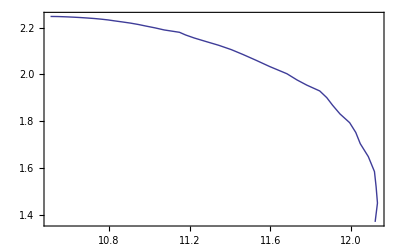

```mathematica
ListPlot[{Table[{TT0[[i]][[5]],TT0[[i]][[6]]},{i,1,Length[TT0]}]},Joined->True,Frame->True,PlotRange->All]
```

```mathematica
Export["../data/MS1.dat",TT];
```

#### GR 2nd order

```mathematica
SetDirectory[NotebookDirectory[]];
rhoi=2.5;
rhof=3.5;
DIM=10;
TT={}{};
dx=(rhof-rhoi)/DIM;
β00=- 4π 4.5;
Monitor[Do[
INT[Pρ[xx 10^15 gcm3],β00, 10^-8 0.030791435175163858,0,1,15,2 10^-3,300,10,10,2];

AppendTo[TT,{Ibar,Qbar,λbar,ρni/(10^14 gcm3)/.r->rc,R/km,MASS,EB,Ωs km,Rg/R,ω1nibefore/omrescal/.r->rc,δR/R,δM/MASS,δEB/EB,Q/(MASS R^2),ecc,charge,charge0,charge2,const}];

,{xx,rhoi,rhof,dx}],IntegerPart[(xx-rhoi)/dx]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Export["../data/FPS_c.dat",TT];
```

```mathematica
TTa=Import["../data/MS1_b.dat","Table"];
```

```mathematica
Export["../data/MS1.dat",Join[TT,TTa]];
```

```mathematica
TT1=TT;
```

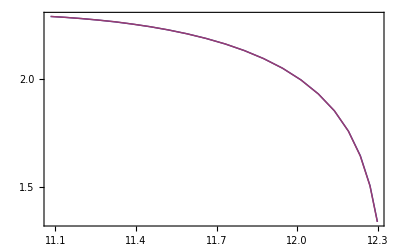

```mathematica
ListLogPlot[{Table[{TT1[[i]][[5]],TT1[[i]][[6]]//Abs},{i,1,Length[TT1]}],Table[{TT2[[i]][[5]],TT2[[i]][[6]]//Abs},{i,1,Length[TT2]}]},Joined->True,Frame->True,PlotRange->All]
```

#### Root Finders (zeroth and 1st order):

```mathematica
SetDirectory[NotebookDirectory[]];
count=0;
β00=- 4π 6;
guess0=0.0016927716623481755;
phi0=10^-3;
(*guess0=0.029850173884166203;*)
Timing[Monitor[
f0[z_?NumberQ]:=INT[Pρ[0.3 10^15 gcm3],β00,z,0,1,15,2 10^-3,500,10,10,1][[1]];
root0=z/.FindRoot[f0[z]-phi0,{z,guess0}];
check0=f0[root0];
{root0,check0,MASS,MASS/R,R,√(4π)charge/MASS},{count}]]
R/km
(*****************************************)
```

{6.17667,{0.00169277,0.001,0.276772,0.0272689,10.1497,0.0304166}}

14.9873

#### TRACKING

```mathematica
SetDirectory[NotebookDirectory[]];
rhoi=0.3;
rhof=2.2;
DIM=80;
TT={}{};
dx=(rhof-rhoi)/DIM;
β00=- 4π 6;(*coupling= β/(4πG)*)
phi0=10^-3;


guess=0.0001733914536534473;(*APR 0.8e15g/cm^3, coupling=-4.5 ; φ0=10^-5*)
guess=0.00004564688088952597;(*FPS 0.8e15g/cm^3, coupling=-4.5 ; φ0=10^-5*)
guess=0.00010274448178702074;(*MS1, 0.5e15g/cm^3, coupling=-4.5 ; φ0=10^-5*)
guess=0.018239269976588677;(*MS1 0.16e15g/cm^3, coupling=-4.5 ; φ0=10^-3*)
guess=0.0018605168366634243;(*FPS 0.5e15g/cm^3, coupling=-4.5 ; φ0=10^-3*)
guess=0.00230584131183285;(*APR 0.5e15g/cm^3, coupling=-4.5 ; φ0=10^-3*)
guess=0.0013854372083242513;(*FPS 0.3e15g/cm^3, coupling=-6 ; φ0=10^-3*)
guess=0.00230584131183285;(*APR 0.3e15g/cm^3, coupling=-6 ; φ0=10^-3*)
Monitor[Do[
count=0;
Monitor[
f0[z_?NumberQ]:=INT[Pρ[xx 10^15 gcm3],β00,z,0,1,15,2 10^-3,300,10,10,1][[1]];
root0=z/.FindRoot[f0[z]-phi0,{z,guess}];
check0=f0[root0];
guess=root0;
{root0,check0},{count}];
(***)
INT[Pρ[xx 10^15 gcm3],β00,root0,0,1,15,2 10^-3,300,10,10,2];
(***)

AppendTo[TT,{Ibar,Qbar,λbar,ρni/(10^14 gcm3)/.r->rc,R/km,MASS,EB,Ωs km,Rg/R,ω1nibefore/omrescal/.r->rc,δR/R,δM/MASS,δEB/EB,Q/(MASS R^2),ecc,charge,charge0,charge2,const,λloveS}];

,{xx,rhoi,rhof,dx}],{IntegerPart[(xx-rhoi)/dx],guess,xx//N,MASS,R/km,charge}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

$Aborted

```mathematica
TT1=Import["../data/APR_coupling_4.5_phi0_1em3.dat","Table"];
```

```mathematica
TTs=TT;
```

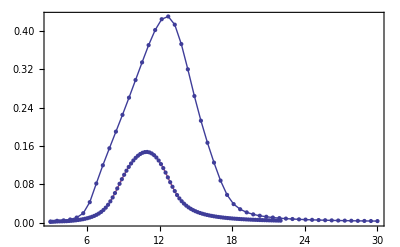

```mathematica
ListPlot[{Table[{TTs[[i]][[4]],TTs[[i]][[16]]//Abs},{i,1,Length[TTs]}],Table[{TT1[[i]][[4]],TT1[[i]][[16]]//Abs},{i,1,Length[TT1]}]},Joined->True,Frame->True,PlotRange->All,Mesh->All]
```

```mathematica
Table[{TT[[i]][[5]],TT[[i]][[16]]//Abs},{i,1,Length[TT]}]
```

{{12.2597,0.},{12.2313,0.},{12.1845,0.},{12.148,0.},{12.0807,0.},{12.0097,0.},{11.9502,0.},{11.8833,0.},{11.8133,0.},{11.7811,0.},{11.6913,0.},{11.617,0.},{11.5573,0.},{11.4876,0.},{11.426,0.},{11.3629,0.},{11.3018,0.},{11.2452,0.},{11.1874,0.},{11.1273,0.},{11.0749,0.}}

```mathematica
Export["../data/APR_coupling_6_phi0_1em3.dat",TT];
```